```mathematica
(*
This Worksheet was written by Charles Barton
please contact him with any questions or comments:
c.j.barton@dl.ac.uk
*)

(*Setup
Very Important!!!

Change SetDirectory command everywhere to be 
..."Mathematica\4.0\AddOns\"...\n\nThe 4.0 often gets eliminated upon saving the file and the code will not run properly\n\n"c:\Program Files\Wolfram Research\Mathematica\4.0\AddOns\StandardPackages\Graphics"
*)

Directory[]
$Path
(*
SetDirectory["c:\Program Files\Wolfram Research\Mathematica.04\AddOns\StandardPackages\Graphics"]
*)
<<FunctionApproximations`
UpdateNotationsInNotebook[]
```

/npdisks/home/cjb18

{/phys/sfw/mathematica/7.0/SystemFiles/Links,/npdisks/home/cjb18/.Mathematica/Kernel,/npdisks/home/cjb18/.Mathematica/Autoload,/npdisks/home/cjb18/.Mathematica/Applications,/usr/share/Mathematica/Kernel,/usr/share/Mathematica/Autoload,/usr/share/Mathematica/Applications,.,/npdisks/home/cjb18,/phys/sfw/mathematica/7.0/AddOns/Packages,/phys/sfw/mathematica/7.0/AddOns/LegacyPackages,/phys/sfw/mathematica/7.0/SystemFiles/Autoload,/phys/sfw/mathematica/7.0/AddOns/Autoload,/phys/sfw/mathematica/7.0/AddOns/Applications,/phys/sfw/mathematica/7.0/AddOns/ExtraPackages,/phys/sfw/mathematica/7.0/SystemFiles/Kernel/Packages,/phys/sfw/mathematica/7.0/Documentation/English/System}

UpdateNotationsInNotebook[]

```mathematica
Print["Write up of theory"]
(* axially symmetric Nuclei can be oriented or aligned

note - the density matrix formalism of Fano is used.  This is because the angular distribution or correlation experiment does not result in a complete knowledge of the individual nuclei or the individual quanta, only ensemble averages are observed.  The statistical knowledge of the orientation of the ensemble of nuclei or quanta is involved, no maximum information is available.  The quantum  mechanical description of such mixed states (e.g. ensembles of particles or quanta) requires incoherent superpositions of pure quantum states. Thus, an esemble cannot be described by state vectors or wavefunctions.  Mixed states must be described by the density matrix formalism.

note - randomly oriented nuclei have rank (λ) = 0

axially symmetric oriented ensemble of nuclei are nuclei where the projection of the rank of the statistical tensors is zero (q = 0) so that the statistical tensors become 
Subscript[ρ, 0]^λ[J]:=∑_(m=-J)^J (-1)^(J+m)(2λ+1)^(1/2)ThreeJSymbol[{J,-m},{J,m},{λ,0}]g[m]

aligned nuclei are an axially symmetric oriented ensemble of nuclei that are invaient under the reversal of the symmetry axis (z -> -z) and the statistical tensors (which are Subscript[ρ, q]^λ[J]) of even rank (λ) are the same (equal) so that (Subscript[ρ, 0]^λ[J] for z = Subscript[ρ, 0]^λ[J] for -z)
 while the odd rank statistical tensors vanish. (The corresponding density matrix has diagonal matrix elements that are symmetric between positive and negative m-values)

A polarized ensemble is not symmetric with respect to the reversal of the symmetry axis and must contain odd and even rank statistical tensors. (at least 1 odd rank statistical tensor must survive)

An orientation of a nuclear ensemble is achieved throught either of two different mechanisms:
1 the interaction of external fields with the static moments of the nuclei.
2 through the absorption or emission and observation of radiation that leads to the formation of the nuclear state under consideration.
In either of the two cases, the interaction mechanism give rise to unequal population m states. The density matrix is then not proportional to the unit matrix and statistical tensors with lambda not equal to 0 do not occur.

The interacting fields generating the ensemble of oriented nuclei can have an axis of cylindrical symmetry.  Such a symmetry axis becomes the z axis of the representation.  The density matrix is then diagonal in this representation and the degree of the nuclear orientation is completely described by the relative populations of the different magnetic substates.

The following statistical tensors describe the axially symmetric oriented ensemble
Subscript[ρ, 0]^λ[J]:=∑_(m=-J)^J (-1)^(J+m)(2λ+1)^(1/2)ThreeJSymbol[{J,-m},{J,m},{λ,0}]g[m]

where g[m], for aligned states,  can be described as a Guassian of width σ around (m=0)
g[m]=constant ⅇ^(-m^2/(2 σ^2))
for so-called oblate alignment, where the magnetic substate populations are weighted toward (m=0) for integer levels and (m=+1/2, -1/2) for half-integer levels.

 the magnetic substate populations can be weighted toward the maximum allowed positive and negative values:
g[m]=constant ⅇ^((-(J-Abs[m])^2)/(2 σ^2))
for prolate alignment.
It there is a continuing weighting of magnetic substate populations from positive to negative then you have polarization, which also implies adding odd values to the tensor rank summations in all the calculations 
g[m]=constant ⅇ^((-(J-m)^2)/(2 σ^2))
is then for polarization.

and the orientation parameter is given by
Subscript[B, λ][J]:=(2J+1)^(1/2)Subscript[ρ, 0]^λ[J] which is also equal to ∑_(m=-J)^J (-1)^(J+m)((2λ+1)(2J+1))^(1/2)ThreeJSymbol[{J,-m},{J,m},{λ,0}]g[m]

Now, the Alignment can be defined in terms of the Subscript[B, 2] or Subscript[ρ, 20] statistical tensor because the effect of the (k=2) term on experimental observables is usually much larger than the (k=4) term. The alignment is defined as
A:=Subscript[ρ, 0]^2[J]/Abs[Subscript[ρ, 0]^2 Max[J]]
for Subscript[ρ, 0]^2 Max[J], this can be calculated to about 10^25 accuracy with (σ=0.1) as the width in the exponential, which is how it will be defined


For two mixed multipoles, L and L' = L+1,(such as M1 and E2 multipole transitions)one usually introduces the
 
amplitude mixing ratio
δ=(<Subscript[J, f]|ML+1|Subscript[J, i]>)/(√(2(L+1) +1))/(<Subscript[J, f]|ML|Subscript[J, i]>)/(√(2(L) +1))


F-coefficients are used to to determing the angular momentum coupling between the two states and the photon quanta. There are generalized F-coefficients which then can reduce to the ordinary F-coefficients when one of the oriented states is random. The ordinary F-coefficients utilizes 3-j and 6-j coupling coefficients to do this. Note that the angular momentum of the oriented state is always written last in 
Subscript[F, λ](LL' Subscript[I, f] Subscript[I, i])
Note that if only 1 electromagnetic multipole moment is involved in the transition then 
L=L' in the F-coefficients

Subscript[F, λ](LL' Subscript[I, f] Subscript[I, i])=(-1^(Subscript[J, i]+Subscript[J, f]-1))((2λ+1)(2L+1)(2 L'+1)(2 Subscript[J, i]+1))^(1/2)ThreeJSymbol[{L,1},{L',-1},{λ,0}]SixJSymbol[{L,L',λ},{Subscript[J, i],Subscript[J, i],Subscript[J, f]}]


With mixing there is now a δ and the Subscript[F, λ] coefficients are now (with L being the electromagnetic multipole of lowest order in the mixing of 2 multipoles):

Subscript[A, λ]={Subscript[F, λ](Subscript[LLI, f] Subscript[I, i])+2 Subscript[δF, λ](LL+1 Subscript[I, f] Subscript[I, i])+δ^2 Subscript[F, λ](L+1L+1 Subscript[I, f] Subscript[I, i])}1/(1+δ^2)

Furthermore, there may be effects that attenuate the gamma ray angular distribution

Subscript[Q, λ]  The finite size of the detector must be taken into account by including the coefficient Subscript[Q, λ] in the directional distribution function. These depend upon the geometry and the λ which are the even order of the Legendre Polynomials

Subscript[U, λ](Subscript[I, unobserved] Subscript[I, i] L)    There may be 1 or more intermediate transition that occure before the gamma ray of interest is observed.  These may lead to a redistribution of the population of the magnetic γsubstates m in the state of interest and the coefficients are 
Subscript[U, λ](Subscript[I, unobserved] Subscript[I, i] L)

If there are several unobserved transitions and they are 
IN SERIES, then the PRODUCTS of Subscript[U, λ](Subscript[I, unobserved] Subscript[I, i] L) are taken

If there are several unobserved transitions and they are 
IN PARELLEL, then the WEIGHTED AVEREAGE of Subscript[U, λ](Subscript[I, unobserved] Subscript[I, i] L) are taken

Subscript[U, λ](Subscript[I, unobserved] Subscript[I, i] L) depends upon the spins of the 2 levels and the angular momentum of the transitions linking them.

Subscript[U, λ](Subscript[I, unobserved] Subscript[I, i] L)=(-1)^(Subscript[I, unobserved]+Subscript[I, i]+λ+L)((2 Subscript[I, unobserved]+1)(2 Subscript[I, i]+1))^(1/2)SixJSymbol[{Subscript[I, unobserved],Subscript[I, unobserved],λ},{Subscript[I, i],Subscript[I, i],L}]

There may also be mixing the in unobserved transition, so when the unobserved transition has a mixing amplitude
Subscript[δ, unobserved]=E(L+1)/M(L) then

Subscript[U, λ](L,L+1)=(Subscript[U, λ](L)+Subscript[δ, unobserved]^2 Subscript[U, λ](L+1))/(1+Subscript[δ, unobserved]^2)

Finally, there can be internal conversion that is a significan decay mode of the transition and this must be taken into account in the expression for the coefficients Subscript[U, λ]

Subscript[U, λ](L,L+1;e,γ)=((1+β)Subscript[U, λ](L)+Subscript[δ, unobserved]^2(1+α)Subscript[U, λ](L+1))/((1+β)+(1+α)Subscript[δ, unobserved]^2)
where α and β are the conversion coefficients of the 
L+1 and L components

Subscript[G, λ]  There can be a perturbation of the angular distribution, but in general this is not observed. This is because the dominant interaction ont he nuclei is that producing the orientation and measurements are invariable made with respect tot he orientation direction which is also the symmetry axis of the system.  However, if tanother interaction is also present, for example a quadrupole interaction in addition to a magnetic interaction, and it has a different symmetry axis, then, depending on their relative strengths, a perturbation may be observed.  Perturbations may also occur when the orientation is produced by a nuclear method, such as beta decay, since any perturbing field will not necessarily be along the symmetry axis.

Laboratory angular distributions of the gamma rays can be shifted from the reference frame of the excited nucleus to the laboratory.  To obtain the distribution in the laboratory, one has to perform the transformation 

Subscript[θ, Lab]=ArcTan[Sin[θ]/(γ(Cos[θ]+β))] 

this accounts for abberation

W(Subscript[θ, Lab])=γ^2(1+β*Cos[θ])^2W(θ)

while the factor in from of W(θ) is the ratio of solid angles from the cm to the lab frame

and where, of course, 

γ=(1+ϵ+ρ)/(√((1+ρ)^2+2ρϵ))

β=√(1+1/γ^2)
Where ρ and ϵ are from the lab experimental parameters:
ρ=Subscript[M, Projectile]/Subscript[M, Target]
ϵ=(Subscript[E, Lab](MeV/nucleon))/(Subscript[m, nucleon] c^2)
*)
```

Write up of theory

Edit input parameters here

M_Projectile=

16

M_Target=

154

E_Lab=

65

ρ=M_Projectile/M_Target

8/77

ϵ=E_Lab/931.49432

0.0697804

β=

0.01

γ=

1.00005

θ_Lab=

ArcTan[(0.99995 Sin[θ])/(0.01+Cos[θ])]

E_photonCM=

1.1

J_i=

4

2

J_f=

2

L=

2

δ=

0.

Guassian magnetic substate distribution width σ =

0.5

ⅇ^(-2. x^2)

{{-4,9.96126×10^-15},{-3,1.19795×10^-8},{-2,0.000263865},{-1,0.106451},{0,0.786571},{1,0.106451},{2,0.000263865},{3,1.19795×10^-8},{4,9.96126×10^-15}}

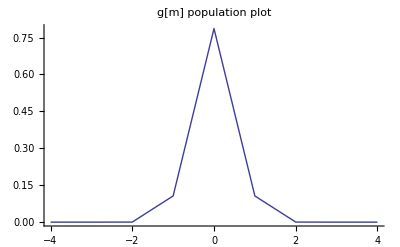

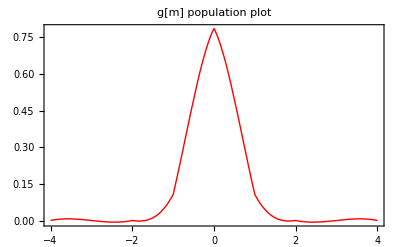

U[λ]= for λ 0 to 10

2.5

20.

1.

157.6

133.57

107.94

94.16

85.84

72.05

6

0.124355

Det #     min angle         max angle

157.6   150.475    164.725

133.57   126.445    140.695

107.94   100.815    115.065

94.16   87.035    101.285

85.84   78.715    92.965

72.05   64.925    79.175

Q[λ]= for λ 0 to 10

ρ[λ] is the statistical tensor which describes the axially symmetric oriented ensemble used to calculate B[λ]

Printing ρ[λ]= for 0 to 10

ClebschGordan::tri: ThreeJSymbol[{4, 4}, {4, -4}, {9, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{4, 3}, {4, -3}, {9, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{4, 2}, {4, -2}, {9, 0}] is not triangular.

General::stop: Further output of ClebschGordan will be suppressed during this calculation.

0.333333

-6.87454×10^-20

-0.367617

-5.28166×10^-19

0.359125

2.92065×10^-18

-0.348492

3.70071×10^-19

0.380377

0

0

B[λ] is the alignment parameter used for each coefficient

Printing B[λ]= for 0 to 10

1.

-2.06236×10^-19

-1.10285

-1.5845×10^-18

1.07737

8.76195×10^-18

-1.04548

1.11021×10^-18

1.14113

0

0

F-coefficients to describe all angular momentum coupling

Printing FLambda[λ]= for 0 to 10

ClebschGordan::tri: ThreeJSymbol[{2, 1}, {3, -1}, {0, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{2, 3, 0}, {4, 4, 2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 1}, {2, -1}, {5, 0}] is not triangular.

SixJSymbol::tri: SixJSymbol[{2, 2, 5}, {4, 4, 2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{2, 1}, {2, -1}, {6, 0}] is not triangular.

General::stop: Further output of ClebschGordan will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{2, 2, 6}, {4, 4, 2}] is not triangular.

General::stop: Further output of SixJSymbol will be suppressed during this calculation.

1.

-0.645497

-0.447702

0.749149

-0.304379

0.

0.

0

0

0

«1 more identical outputs»

a[λ]are the final coefficients for Legrende Polynomials

Printing a[λ]= for 0 to 10 (coefficients for Legrende Polynomials)

1.

1.32611×10^-19

0.488045

-1.1597×10^-18

-0.315415

0.

0.

0

0

0

«1 more identical outputs»

Maximum Alignment Coefficient Calculations

ClebschGordan::tri: ThreeJSymbol[{4, 4}, {4, -4}, {9, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{4, 3}, {4, -3}, {9, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{4, 2}, {4, -2}, {9, 0}] is not triangular.

General::stop: Further output of ClebschGordan will be suppressed during this calculation.

Alignment (α_2 from Yamasaki Coefficients)=

Set::wrsym: Symbol Alignment is Protected.

-0.967748

σ/J_i =

0.125

All alignment Coefficients α[λ] = from 0 to 10

Power::infy: Infinite expression 1/0``2184.316074911642 encountered.

Power::infy: Infinite expression 1/0``2183.9705743743093 encountered.

Power::infy: Infinite expression 1/0``2183.8078797035478 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

1.

ComplexInfinity

-0.967748

ComplexInfinity

0.892699

ComplexInfinity

-0.775345

ComplexInfinity

0.616461

Indeterminate

Indeterminate

NORMALIZE TO A0 SO THAT A[0] = 1

Distribution

1.+1.32611×10^-19 Cos[θ]+0.244022 (-1+3 Cos[θ]^2)-5.79851×10^-19 (-3 Cos[θ]+5 Cos[θ]^3)-0.0394268 (3-30 Cos[θ]^2+35 Cos[θ]^4)+0. (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)+0. (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)

Point-like Detector Distribution

1.+1.33125×10^-19 Cos[θ]+0.246875 (-1+3 Cos[θ]^2)-5.93512×10^-19 (-3 Cos[θ]+5 Cos[θ]^3)-0.0409913 (3-30 Cos[θ]^2+35 Cos[θ]^4)+0. (15 Cos[θ]-70 Cos[θ]^3+63 Cos[θ]^5)+0. (-5+105 Cos[θ]^2-315 Cos[θ]^4+231 Cos[θ]^6)

Simple Distributioin of Simplify[∑_(λ = 0)^10 (a[λ] LegendreP[λ, Cos[θ]])/a[0]]

0.637697+1.87216×10^-18 Cos[θ]+1.91487 Cos[θ]^2-2.89925×10^-18 Cos[θ]^3-1.37994 Cos[θ]^4+0. Cos[θ]^5+0. Cos[θ]^6

```mathematica
Print["Edit input parameters here"]
Null

Do[Q[λ]=0.,{λ,0,10,1}]
Do[U[λ]=0.,{λ,0,10,1}]
(*
Do[g[m]=0,{m,-Subscript[J, i],Subscript[J, i],1}]
Do[gMax[m]=0,{m,-Subscript[J, i],Subscript[J, i],1}]
both now defined just after J_i is defined below
*)
Do[RhoLambda[λ]=0,{λ,0,10,1}]
Do[B[λ]=0,{λ,0,10,1}]
Do[FLambda[λ]=0,{λ,0,10,1}]
Do[α[λ]=0,{λ,0,10,1}]
Do[a[λ]=0,{λ,0,10,1}]




Print["\!\(\*\nStyleBox[\(M\_Projectile\),\nFontColor->RGBColor[1, 0, 0]]\)="]
Subscript[M, Projectile]=16
Print["\!\(\*\nStyleBox[\(M\_Target\),\nFontColor->RGBColor[1, 0, 0]]\)="]
Subscript[M, Target]=154
Print["\!\(\*\nStyleBox[\(E\_Lab\),\nFontColor->RGBColor[1, 0, 0]]\)="]
Subscript[ⅇ, Lab]=65

Print["ρ=\!\(\*FractionBox[SubscriptBox[\(M\), \(Projectile\)], SubscriptBox[\(M\), \(Target\)]]\)"]
ρ=Subscript[M, Projectile]/Subscript[M, Target]
Print["ϵ=\!\(\*FractionBox[SubscriptBox[\(E\), \(Lab\)], \(931.49432\)]\)"]
ϵ=Subscript[ⅇ, Lab]/931.49432

(* calculate gamma and beta FOR ONLY THE CASE OF INELASTIC SCATTERING, LIKE INTERMEDIATE ENERGY COULOMB EXCITATION *)
(*
Print["γ="] 
γ=(1+ϵ+ρ)/(√((1+ρ)^2+2 ρ ϵ))
Print["β="] 
β=Sqrt[1-1/γ^2]
*)

(* or enter beta for ALL OTHER CASES *)
(* *)
Print["β="]
β=0.01(*James Smallcombe*)
(*β=0.027*)(*Adam Hecht*)
(*β=0.5*)(*RISING*)
(*β=0.03313*)
Print["γ="]
γ=√(1/(1-β^2))
(* *)

Print["\!\(\*SubscriptBox[\(θ\), \(Lab\)]\)="]
Subscript[θ, Lab]=ArcTan[Sin[θ]/(γ (Cos[θ]+β))]
Print["\!\(\*\nStyleBox[\(E\_photonCM\),\nFontColor->RGBColor[1, 0, 0]]\)="]
Subscript[ⅇ, photonCM]=1.1 (* MeV *)

(* GAMMA ANGULAR DISTRIBUTIONS *)
(*IMPORTANT - enter half-spins as fractions...not real numbers*)
Print["\!\(\*\nStyleBox[\(J\_i\),\nFontColor->RGBColor[1, 0, 0]]\)="]
Subscript[J, i]=4 (* Spin of initial state *)
Subscript[J, 2]=2 (* Spin of initial state for second transition *)
Print["\!\(\*\nStyleBox[\(J\_f\),\nFontColor->RGBColor[1, 0, 0]]\)="]
Subscript[J, f]=2
Print["\!\(\*\nStyleBox[\"L\",\nFontColor->RGBColor[1, 0, 0]]\)="]
L=2 (* gamma antular momentum is also the one of lowest multipole order gamma if there is mixing *)
(*see further along for m-state distribution functions*)

Print["\!\(\*\nStyleBox[\"δ\",\nFontColor->RGBColor[1, 0, 0]]\)="]

(*  mixing ratio which is δ=(<Subscript[J,f]|ML+1|Subscript[J,i]>)/Sqrt[2(L+1)+1]/(<Subscript[J,f]|ML|Subscript[J,i]>)/Sqrt[2(L)+1]  *)
δ=0.0

(**)
Print["Guassian magnetic substate distribution width \!\(\*\nStyleBox[\"σ\",\nFontColor->RGBColor[1, 0, 0]]\) ="]
σ=0.5 (* sigma_ Jg Mg Ji Mi  *)
(* Width of Guassian magnetic substate population distribution of the initial state *)

Do[g[m]=0,{m,-Subscript[J,i],Subscript[J,i],1}]
Do[gMax[m]=0,{m,-Subscript[J,i],Subscript[J,i],1}]
(**)
(* OBLATE ALIGNMENT  (M=0) *)
(* Guassian m-state distribution sigma = 1.1 -> 1.3 is not unreasonable for fusion-evaporation experiments *)
(**)
Do[gunnorm[m]=ⅇ^(-m^2/(2 σ^2)),{m,-Subscript[J, i],Subscript[J, i],1}]
gunnormplot[x]=ⅇ^(-x^2/(2 σ^2))
Do[gMaxunnorm[m]=ⅇ^(-m^2/(2 0.01^2)),{m,-Subscript[J, i],Subscript[J, i],1}]
(**)
(* These are test statements from Stuchbery NuclPhysA to be placed 
near the alignment output near the plot section here
Print["\!\(\*
StyleBox[\"RhoLambda2\",\nFontColor->RGBColor[1, 0, 0]]\)\!\(\*
StyleBox[\" \",\nFontColor->RGBColor[1, 0, 0]]\)\!\(\*
StyleBox[\"Stuchbery\",\nFontColor->RGBColor[1, 0, 0]]\)="]
RhoLambda2Stuchbery=∑_(m=-Subscript[J, i])^Subscript[J, i] FractionBox[2(3 m^2-SubscriptBox[J,i](Subscript[J, i]+1)),SuperscriptBox[((2 Subscript[J, i]+3)(2 Subscript[J, i]+2)2SubscriptBox[J,i](2 Subscript[J, i]-1)),1/2]]g[m]Print["\!\(\*
StyleBox[\"RhoTestMax\",\nFontColor->RGBColor[1, 0, 0]]\)\!\(\*
StyleBox[\" \",\nFontColor->RGBColor[1, 0, 0]]\)\!\(\*
StyleBox[\"Stuchbery\",\nFontColor->RGBColor[1, 0, 0]]\)="]RhoLambda2MaxStuchbery=N[(-2 Subscript[J, \
i](Subscript[J, i]+1))/((2Subscript[J, i]+3)(2Subscript[J, \
i]+2)2Subscript[J, i](2Subscript[J, i]-1))^(1/2)]
Print["\!\(\*
StyleBox[\"Alignment\",\nFontColor->RGBColor[1, 0, 0]]\)\!\(\*
StyleBox[\" \",\nFontColor->RGBColor[1, 0, 0]]\)\!\(\*
StyleBox[\"Stuchbery\",\nFontColor->RGBColor[1, 0, 0]]\)"]
AlignmentStuchbery=∑_(m=-Subscript[J, i])^Subscript[J, i] FractionBox[(3 m^2-SubscriptBox[J,i](Subscript[J, i]+1)),SubscriptBox[J,i](Subscript[J, i]+1)]g[m]
dummy3=RhoLambda2Stuchbery/Abs[RhoLambda2MaxStuchbery]
*)


(* PROLATE ALIGNMENT (abs[m]=max)  *)
(*
Do[gunnorm[m]=ⅇ^(-(Subscript[J, i]-Abs[m])^2/(2 σ^2)),{m,-Subscript[J, i],Subscript[J, i],1}] 
gunnormplot[x]=ⅇ^(-(Subscript[J, i]-Abs[x])^2/(2 σ^2)) 
Do[gMaxunnorm[m]=ⅇ^(-(Subscript[J, i]-Abs[m])^2/(2 0.01^2)),{m,-Subscript[J, i],Subscript[J, i],1}]
*)


(* POLARIZATION (m varies uniformly from min to max)  *)
(*
Do[gunnorm[m]=ⅇ^(-(Subscript[J, i]-m)^2/(2 σ^2)),{m,-Subscript[J, i],Subscript[J, i],1}]  (* polarization note that m=0  *)
gunnormplot[x]=ⅇ^(-(Subscript[J, i]-x)^2/(2 σ^2)) 
Do[gMaxunnorm[m]=ⅇ^(-(Subscript[J, i]-m)^2/(2 0.01^2)),{m,-Subscript[J, i],Subscript[J, i],1}]
*)

(* or you can enter g[m] here *)
(*This can be from cross sections to the magnetic substates populated in single-nucleon knowckout reactions since these can be calculated*)
(*
Print["hand-input g[m]"] 
gunnorm[5/2]=gunnorm[-5/2]=12.8 
gunnorm[3/2]=gunnorm[-3/2]=6.6 
gunnorm[1/2]=gunnorm[-1/2]=5.7 
(* determine which gMaxunnorm to use - for oblate or prolate or polarization *)
Do[gMaxunnorm[m]=ⅇ^(-(Subscript[J, i]-Abs[m])^2/(2 0.01^2)),{m,-Subscript[J, i],Subscript[J, i],1}] 
gunnormplot=1+x+x^2  (*actually will not work for plotting purposes below*)
*)

(* ISOTROPIC m-state distribution  *)
(*
Do[gunnorm[m]=1/(2 Subscript[J, i]+1),{m,-Subscript[J, i],Subscript[J, i],1}]
Do[gMaxunnorm[m]=1/(2 Subscript[J,i]+1),{m,-Subscript[J,i],Subscript[J,i],1}]
*)

(* Total alignment with m=0 such as with CoulEx and detection of particle at 180 degrees  *)
(*
Do[gunnorm[m]=0,{m,-Subscript[J, i],Subscript[J, i],1}] 
gunnorm[0]=1
*)

(* Now normalize m-state distribution *)
NormalizeGm:=∑_(m=-Subscript[J, i])^Subscript[J, i] gunnorm[m]
NormalizeGmMax:=∑_(m=-Subscript[J, i])^Subscript[J, i] gMaxunnorm[m]
Do[g[m]=gunnorm[m]/NormalizeGm,{m,-Subscript[J, i],Subscript[J, i],1}]
Do[gMax[m]=gMaxunnorm[m]/NormalizeGmMax,{m,-Subscript[J, i],Subscript[J, i],1}]
(*
Print["list of magnetic substates from -\!\(\*SubscriptBox[\(J\), \(i\)]\) to \!\(\*SubscriptBox[\(J\), \(i\)]\)"] 
Do[Print[m],{m,-Subscript[J, i],Subscript[J, i],1}] Print["list of normalized magnetic substate populations from -\!\(\*SubscriptBox[\(J\), \(i\)]\) to \!\(\*SubscriptBox[\(J\), \(i\)]\)"] 
Do[Print[g[m]],{m,-Subscript[J, i],Subscript[J, i],1}] 
plottableg=Table[g[m],{m,-Subscript[J, i],Subscript[J, i],1}] 
ListPlot[plottableg]
*)

plottableg=Table[{m,g[m]},{m,-Subscript[J, i],Subscript[J, i],1}]
ListPlot[plottableg,Joined->True,PlotLabel->"g[m] population plot"]

Plot[Evaluate[Interpolation[plottableg]][x],{x,-Subscript[J, i],Subscript[J, i]},Frame->True,PlotRange->All,AxesOrigin->{0,0},PlotLabel->"g[m] population plot",PlotStyle->{RGBColor[1,0,0]}]
(* *)


(* UNOBSERVED TRANSITIONS  (see above discussion in theory ) must add a new expression if interanl conversion is the unobserved transition  *)
(* UNOBSERVED FEEDING TRANSITIONS  1=NONE  *)
Print["U[λ]= for λ 0 to 10"]
Do[U[λ]=1.,{λ,0,10,1}]
(*Do[Print[U[λ]],{λ,0,10,1}]*)
(*
Subscript[ⅈ, unobserved]=4 (* 3 FOR TEST *)
Subscript[ⅈ, i]=Subscript[J, i] Subscript[L, M]=2 (*PHOTON ANGULAR MOMENTUM OR L OF M(L) IF MIMIXING  (1)  *)
Subscript[δ, unobserved]=0  (* delta_unobserved=E(L+1)/M(L)  (1)  *)Do[U[λ]=1/(1+Subscript[δ, unobserved]^2)((-1)^(Subscript[ⅈ, unobserved]+Subscript[ⅈ, i]+λ+Subscript[L, M]) √((2 Subscript[ⅈ, unobserved]+1) (2 Subscript[ⅈ, i]+1)) Check[SixJSymbol[{Subscript[ⅈ, unobserved],Subscript[ⅈ, unobserved],λ},{Subscript[ⅈ, i],Subscript[ⅈ, i],Subscript[L, M]}],0]+δ^2 (-1)^(Subscript[ⅈ, unobserved]+Subscript[ⅈ, i]+λ+(Subscript[L, M]+1)) √((2 Subscript[ⅈ, unobserved]+1) (2 Subscript[ⅈ, i]+1)) Check[SixJSymbol[{Subscript[ⅈ, unobserved],Subscript[ⅈ, unobserved],λ},{Subscript[ⅈ, i],Subscript[ⅈ, i],Subscript[L, M]+1}],0]),{λ,0,10,1}] Do[Print[U[λ]],{λ,0,10,1}]
*)



(* Finite size of the detector attenuation effect   1= no effect  *)
(* 1= no effect as if a point detector *)
(*
Print["Q[λ]= for λ 0 to 10"]
Do[Q[λ]=1.,{λ,0,10,1}]
Do[Print[Q[λ]],{λ,0,10,1}]
*)

(* For a right cylindrical detector with its axis lying along the source-detector axis the normalized attenuation factor, Q[λ], can be written as Q[λ]=J[λ]/J[0]  This is from Hamilton in Hamilton's book equation 14.4  *)
(* efficiency of the detector as a function of the entrance angle ϕ from the axis of the detector to the source  *)

DetectorRadius=2.5 (* radius in cm *)
DetectorDistance=20. (* distance in cm *)
eff[ϕ]=1. (* efficiency normalized to 1.0  *)
(*detector to target distance (typically 25 cm)*)(*in degrees since used for interpolation in plot section*)
(*Jurosphere detector angles*)
(**)
θDet[1]=157.6
θDet[2]=133.57
θDet[3]=107.94
θDet[4]=94.16
θDet[5]=85.84
θDet[6]=72.05
DetectorNumber=6
(**)

(*Rising angles as measured by design from Simpson and Griffiths*)
(*put detector angles here:*)
(* YRAST Ball  *)
(*
θDet[1]=50
θDet[2]=90
θDet[3]=126
θDet[4]=160
DetectorNumber=4
*)


MaxEntryAngle=ArcTan[DetectorRadius/DetectorDistance]
Do[θDetMin[x]=1/180 θDet[x] π-MaxEntryAngle,{x,1,DetectorNumber,1}]
Do[θDetMax[x]=1/180 θDet[x] π+MaxEntryAngle,{x,1,DetectorNumber,1}]
Do[θDetMinDeg[x]=θDet[x]-(MaxEntryAngle 180)/π,{x,1,DetectorNumber,1}]
Do[θDetMaxDeg[x]=θDet[x]+(MaxEntryAngle 180)/π,{x,1,DetectorNumber,1}]
Print["Det #     min angle         max angle"]
Do[Print[θDet[x],"   ",θDetMinDeg[x],"    ",θDetMaxDeg[x]],{x,1,DetectorNumber,1}]

Do[J[λ]=∫_0^MaxEntryAngle LegendreP[λ,Cos[ϕ]] eff[ϕ] Sin[ϕ]ⅆϕ,{λ,0,10,1}]

Print["Q[λ]= for λ 0 to 10"]
Do[Q[λ]=J[λ]/J[0],{λ,0,10,1}]
(*Do[Print[Q[λ]],{λ,0,10,1}]*)


(* FOR COEFFICIENTS OF LEGRENDRE POLYNOMIALS  *)
Print["ρ[λ] is the statistical tensor which describes the axially symmetric oriented ensemble used to calculate B[λ]"]
Print["Printing ρ[λ]= for 0 to 10"]
Do[RhoLambda[λ]=∑_(m=-Subscript[J, i])^Subscript[J, i] (-1)^(Subscript[J, i]+m) √(2 λ+1) Check[ThreeJSymbol[{Subscript[J, i],-m},{Subscript[J, i],m},{λ,0}],0] g[m],{λ,0,10,1}]
Do[Print[RhoLambda[λ]],{λ,0,10,1}]

Print["B[λ] is the alignment parameter used for each coefficient"]
Print["Printing B[λ]= for 0 to 10"]
Do[B[λ]=√(2 Subscript[J, i]+1) RhoLambda[λ],{λ,0,10,1}]
Do[Print[B[λ]],{λ,0,10,1}]

Print["F-coefficients to describe all angular momentum coupling"]
Print["Printing FLambda[λ]= for 0 to 10"]
Do[FLambda[λ]=1/(1+δ^2)(-1^(Subscript[J, i]+Subscript[J, f]-1) √((2 λ+1) (2 L+1) (2 L+1) (2 Subscript[J, i]+1)) Check[ThreeJSymbol[{L,1},{L,-1},{λ,0}],0] Check[SixJSymbol[{L,L,λ},{Subscript[J, i],Subscript[J, i],Subscript[J, f]}],0]+2 δ (-1^(Subscript[J, i]+Subscript[J, f]-1)) √((2 λ+1) (2 L+1) (2 (L+1)+1) (2 Subscript[J, i]+1)) Check[ThreeJSymbol[{L,1},{L+1,-1},{λ,0}],0] Check[SixJSymbol[{L,L+1,λ},{Subscript[J, i],Subscript[J, i],Subscript[J, f]}],0]+δ^2 (-1^(Subscript[J, i]+Subscript[J, f]-1)) √((2 λ+1) (2 (L+1)+1) (2 (L+1)+1) (2 Subscript[J, i]+1)) Check[ThreeJSymbol[{L+1,1},{L+1,-1},{λ,0}],0] Check[SixJSymbol[{L+1,L+1,λ},{Subscript[J, i],Subscript[J, i],Subscript[J, f]}],0]),{λ,0,10,1}]
Do[Print[FLambda[λ]],{λ,0,10,1}]

(*Do[gunnorm[m] =0,{m,-Subscript[J, i],Subscript[J, i],1}]*)

(* DISTRIBUTION  *)
(* a_λ  *)
Print["a[λ]are the final coefficients for Legrende Polynomials"]
Print["Printing a[λ]= for 0 to 10 (coefficients for Legrende Polynomials)"]
Do[a[λ]=B[λ] FLambda[λ] Q[λ] U[λ],{λ,0,10,1}]
Do[Print[a[λ]],{λ,0,10,1}]


(* or you can enter Subscript[a, λ] here *)
(*
a[0]=1.
a[1]=0 
a[2]=0.3 
a[3]=0 
a[4]=-0.15
*)


(* CM REFERENCE FRAME PLOTS  *)
(*First,do alignment plots with RhoLambda2/Abs[RhoLambda2Max]*)
Print["Maximum Alignment Coefficient Calculations"]
Do[RhoLambdaMax[λ]=∑_(m=-Subscript[J, i])^Subscript[J, i] (-1)^(Subscript[J, i]+m) √(2 λ+1) Check[ThreeJSymbol[{Subscript[J, i],-m},{Subscript[J, i],m},{λ,0}],0] gMax[m],{λ,0,10,1}]
Print["\!\(\*\nStyleBox[\"Alignment\",\nFontColor->RGBColor[1, 0, 0]]\) (\!\(\*SubscriptBox[\(α\), \(2\)]\) from Yamasaki Coefficients)="]
Alignment=RhoLambda[2]/Abs[RhoLambdaMax[2]]
Print["σ/\!\(\*SubscriptBox[\(J\), \(i\)]\) ="]
dummy1=σ/Subscript[J, i]
Print["All alignment Coefficients α[λ] = from 0 to 10"]
Do[α[λ]=RhoLambda[λ]/Abs[RhoLambdaMax[λ]],{λ,0,10,1}]
Do[Print[α[λ]],{λ,0,10,1}]


(* NORMALIZE TO A0 SO THAT A[0]=1  *)
Print["NORMALIZE TO A0 SO THAT A[0] = 1"]
Print["Distribution"]
Distribution=∑_(λ=0)^10 (a[λ] LegendreP[λ,Cos[θ]])/a[0]
Print["Point-like Detector Distribution"]
PointDetDistribution=∑_(λ=0)^10 (Q[0] a[λ] LegendreP[λ,Cos[θ]])/(a[0] Q[λ])
Print["Simple Distributioin of Simplify[∑_(λ = 0)^10 (a[λ] LegendreP[λ, Cos[θ]])/a[0]]"]

SimpleDistribution=Simplify[∑_(λ=0)^10 (a[λ] LegendreP[λ,Cos[θ]])/a[0]]

(*not-normalize to a0 so that a0 could now be-1*)(*Not Used in analysis of experimental data*)
(*
Distribution=(∑_(λ=0)^10 a[λ] LegendreP[λ,Cos[θ]]) (SimpleDistribution=Simplify[∑_(λ=0)^10 a[λ] LegendreP[λ,Cos[θ]]])
*)
```

Alignment (α_2 from Yamasaki Coefficients)=

Set::wrsym: Symbol Alignment is Protected.

-0.967748

σ/J_i =

0.125

{{-4,9.96126×10^-15},{-3,1.19795×10^-8},{-2,0.000263865},{-1,0.106451},{0,0.786571},{1,0.106451},{2,0.000263865},{3,1.19795×10^-8},{4,9.96126×10^-15}}

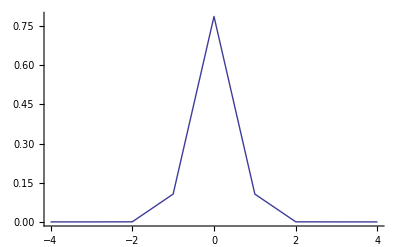

-Graphics-

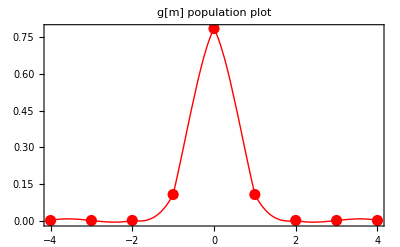

End

```mathematica
(* PLOTS *)
Print["\!\(\*\nStyleBox[\"Alignment\",\nFontColor->RGBColor[1, 0, 0]]\) (\!\(\*SubscriptBox[\(α\), \(2\)]\) from Yamasaki Coefficients)="]
Alignment=RhoLambda[2]/Abs[RhoLambdaMax[2]]
Print["σ/\!\(\*SubscriptBox[\(J\), \(i\)]\) ="]
dummy1=σ/Subscript[J, i]
plottableg=Table[{m,g[m]},{m,-Subscript[J, i],Subscript[J, i],1}]

ListPlot[plottableg,Joined->True]

Plot[Evaluate[Interpolation[plottableg]][x],{x,-Subscript[J, i],Subscript[J, i]},Frame->True,PlotRange->All,AxesOrigin->{0,0},PlotLabel->"g[m] population plot",PlotStyle->{RGBColor[1,0,0]}]


(* Fit is done poorly here and is ignored in favor of above interpolation *)
(*
dummy=Fit[plottableg,gunnormplot[x],{x}] (dummy2=gunnormplot[x]) Print["g[m] population plot for selected population mechanism (oblate aligned,prolate aligned, polarized, individual..."] Plot[dummy gunnormplot[x],{x,-Subscript[J, i],Subscript[J, i]},PlotLabel->"g[m] population plot"]
*)

Show[
Plot[Evaluate[Interpolation[plottableg]][x],{x,-Subscript[J, i],Subscript[J, i]},Frame->True,PlotRange->All,AxesOrigin->{0,0},PlotLabel->"g[m] population plot",PlotStyle->{RGBColor[1,0,0]}],
ListPlot[plottableg,PlotStyle->{Hue[0],PointSize[0.02]}]
]

Print["End"]
```

W(θ_nuclear) versus θ_nuclear for a Point-like detector

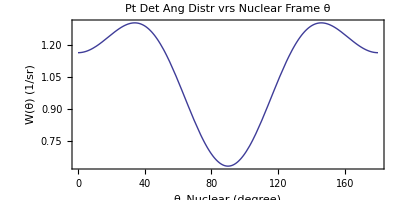

W(θ_nuclear) versus θ_nuclear for the real detector as input

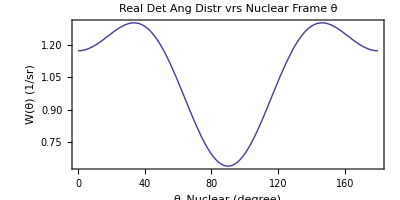

W(θ_nuclear) versus θ_nuclear for a Point-like detector and the real detector as input (2 curves are shown)

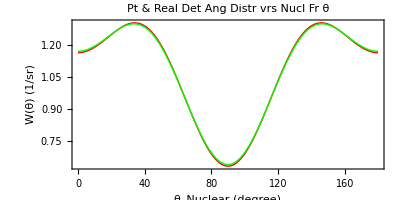

W(θ_nuclear)_Real/W(θ_nuclear)_PointLike versus θ_nuclear (like percent difference between distributions)

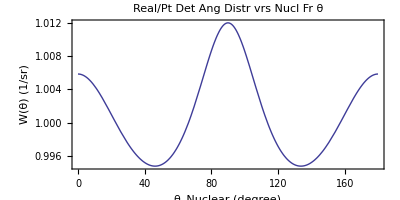

Polar Plot of W(θ_nuclear) versus θ_nuclear for point-like detector

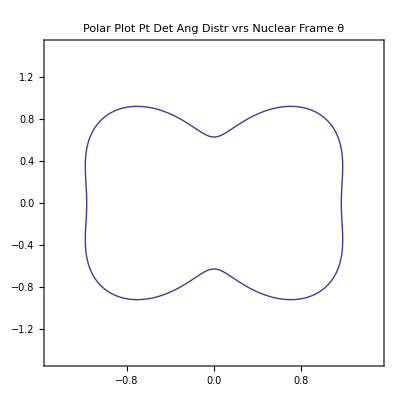

W(θ_nuclear) versus θ_nuclear for the real detector as input

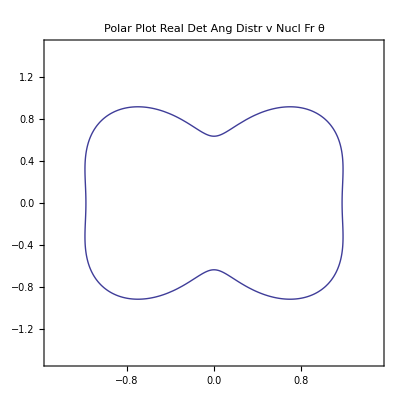

End

```mathematica
Print["W(θ_nuclear) versus θ_nuclear for a Point-like detector"]
ParametricPlot[{(180/π)*θ,PointDetDistribution},{θ,0,π},
Frame->True, PlotRange->All,AxesOrigin->{0,0},AspectRatio->1/2,
PlotLabel-> "Pt Det Ang Distr vrs Nuclear Frame θ",
FrameLabel->{"θ_Nuclear (degree)","W(θ) (1/sr)"}]

Print["W(θ_nuclear) versus θ_nuclear for the real detector as input"]
ParametricPlot[{(180/π)*θ,Distribution},{θ,0,π},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},AspectRatio->1/2,
PlotLabel-> "Real Det Ang Distr vrs Nuclear Frame θ",
FrameLabel->{"θ_Nuclear (degree)","W(θ) (1/sr)"}]

Print["W(θ_nuclear) versus θ_nuclear for a Point-like detector and the real detector as input (2 curves are shown)"]
ParametricPlot[{{(180/π)*θ,PointDetDistribution},{(180/π)*θ,Distribution}},{θ,0,π},
Frame->True, PlotRange->All,
AspectRatio->1/2,
PlotLabel-> "Pt & Real Det Ang Distr vrs Nucl Fr θ ",
FrameLabel->{"θ_Nuclear (degree)","W(θ) (1/sr)"},
PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,1,0]}}]

Print["W(θ_nuclear)_Real/W(θ_nuclear)_PointLike versus θ_nuclear (like percent difference between distributions)"]
ParametricPlot[{(180/π)*θ,Distribution/PointDetDistribution},{θ,0,π},
Frame->True, PlotRange->All,
AspectRatio->1/2,
PlotLabel-> "Real/Pt Det Ang Distr vrs Nucl Fr θ ",
FrameLabel->{"θ_Nuclear (degree)","W(θ) (1/sr)"}]

Print["Polar Plot of W(θ_nuclear) versus θ_nuclear for point-like detector"]
PolarPlot[PointDetDistribution,{θ,0,2π},
Frame->True,PlotRange->All,
PlotLabel-> "Polar Plot Pt Det Ang Distr vrs Nuclear Frame θ"]

Print["W(θ_nuclear) versus θ_nuclear for the real detector as input"]
PolarPlot[Distribution,{θ,0,2π},
Frame->True,PlotRange->All,
PlotLabel-> "Polar Plot Real Det Ang Distr v Nucl Fr θ"]

Print["End"]
```

Laboratory Frame Plots

W(θ_lab) versus θ_lab for point-like detector

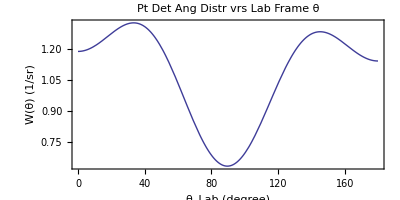

W(θ_lab) versus θ_lab for point-like detector near minimum (between π/3 and 2π/3)

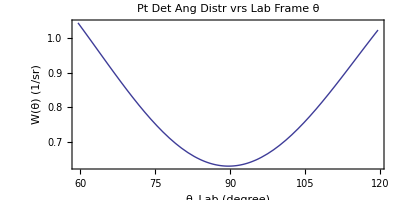

Point Detector Distribution in Lab Frame from List Points

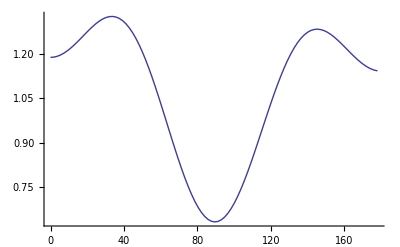

Point Detector Distribution in Lab Frame from List Interpolation

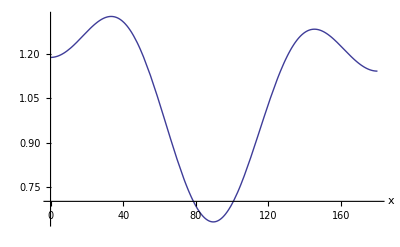

Point Detector Distribution in Nuclear Frame from List Points

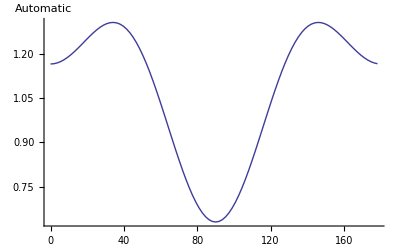

Point Detector Distribution in Nuclear Frame from List Interpolation

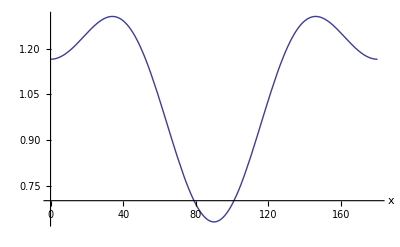

attempt at graphics divide

InterpolatingFunction[{{5.67257×10^-10,178.182}},<>]

InterpolatingFunction[{{5.72958×10^-10,178.2}},<>]

InterpolatingFunction[{{5.72958×10^-10,178.2}},<>]

Plot of W(lab) and W(nuc) Point Detector Angular Distribution vrs ϑ (in each frame)

Point Detector Distribution in NUCLEAR FRAME is RED, in LABORATORY FRAME is GREEN

Plot::axes: Value of option Axes -> Automatic is not True, False, or a length-two list of True or False.

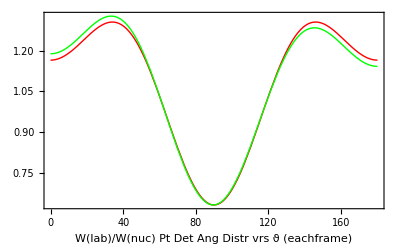

W(lab)/W(nuc) Point Detector Angular Distribution vrs ϑ (in each frame)

similar to error in W(angle) if relativistic effects are not considered

InterpolatingFunction::dmval: Input value {891/5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

Plot::axes: Value of option Axes -> Automatic is not True, False, or a length-two list of True or False.

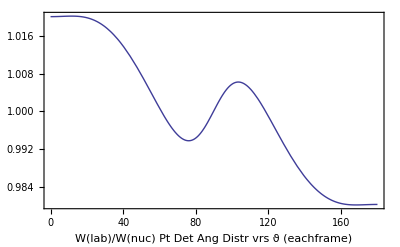

W(θ) for lab and nuclear frame for given detector angles and geometry

IntDet is Real Detector average W(θ) in nuclear frame (integrated from point det in nuclear frame, should be same as real det w(theta) )

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

Detθ   WNuclear    WRealDetNucl   Ratio(Real/Pt)   WNuclInt    Ratio(Int/Real)

157.6   1.26612   1.26624   1.0001   1.26828   1.00162

133.57   1.2424   1.23594   0.994802   1.23233   0.997079

107.94   0.804179   0.806953   1.00345   0.807055   1.00013

94.16   0.640482   0.647737   1.01133   0.65008   1.00362

85.84   0.640482   0.647737   1.01133   0.65008   1.00362

72.05   0.804353   0.807122   1.00344   0.807222   1.00012

End

```mathematica
(*Laboratory Frame Plots*)
Print["Laboratory Frame Plots"]
(*normalize to a0 so that a0=1*)
LabTest:=If[ArcTan[Sin[θ]/(γ*(Cos[θ]+β))]≥0,ArcTan[Sin[θ]/(γ*(Cos[θ]+β))],π+ArcTan[Sin[θ]/(γ*(Cos[θ]+β))]]
Print["W(\!\(\*SubscriptBox[\"θ\", \"lab\"]\)) versus \!\(\*SubscriptBox[\"θ\", \"lab\"]\) for point-like detector"]
ParametricPlot[{LabTest*(180/π),γ^2*(1+β*Cos[θ])^2*PointDetDistribution},{θ,0,π},Frame->True,PlotRange->All,AxesOrigin->{0,0},AspectRatio->1/2,PlotLabel->"Pt Det Ang Distr vrs Lab Frame θ",FrameLabel->{"\!\(\*SubscriptBox[\"θ\", \"Lab\"]\) (degree)","W(θ) (1/sr)"}]

Print["W(\!\(\*SubscriptBox[\"θ\", \"lab\"]\)) versus \!\(\*SubscriptBox[\"θ\", \"lab\"]\) for point-like detector near minimum (between π/3 and 2π/3)"]
ParametricPlot[{LabTest*(180/π),γ^2*(1+β*Cos[θ])^2*PointDetDistribution},{θ,π/3,2 π/3},Frame->True,PlotRange->All,AxesOrigin->Automatic,  AspectRatio->1/2,PlotLabel->"Pt Det Ang Distr vrs Lab Frame θ",FrameLabel->{"\!\(\*SubscriptBox[\"θ\", \"Lab\"]\) (degree)","W(θ) (1/sr)"}]

(*error if lab frame is ignored for beta*)
(*point det distribution in lab frame:*)
dummy1000:=Table[{LabTest*180/π,γ^2*(1+β*Cos[θ])^2*PointDetDistribution},{θ,0.00000000001,π-0.00000000001,π/100}]
(*point det distribution in nuclear frame:*)
dummy1010:=Table[{θ*180/π,PointDetDistribution},{θ,0.00000000001,π-0.00000000001,π/100}]
(*real det distribution in nuclear frame:*)
dummy1020:=Table[{θ*180/π,Distribution},{θ,0.00000000001,π-0.00000000001,π/100}]
(**)
Print["Point Detector Distribution in Lab Frame from List Points"]
ListPlot[dummy1000,Joined->True]
Print["Point Detector Distribution in Lab Frame from List Interpolation"]
Plot[Evaluate[Interpolation[dummy1000]][x],{x,0,180},AxesLabel-> Automatic]
Print["Point Detector Distribution in Nuclear Frame from List Points"]
ListPlot[dummy1010,Joined->True, AxesLabel->Automatic]
Print["Point Detector Distribution in Nuclear Frame from List Interpolation"]
Plot[Evaluate[Interpolation[dummy1010]][x],{x,0,180},AxesLabel->Automatic]

Print["attempt at graphics divide"]
(**)
(*point det distribution in lab frame:*)
dummy2000=Interpolation[dummy1000]
(*point det distribution in nuclear frame:*)
dummy2010=Interpolation[dummy1010]
(*real det distribution in nuclear frame:*)
dummy2020=Interpolation[dummy1020]
(*ratio of W (lab) to W (nuclear)*)
dummy4000:=Table[{θ,dummy2000[θ]/dummy2010[θ]},{θ,0,180,180/100}]

Print["Plot of W(lab) and W(nuc) Point Detector Angular Distribution vrs ϑ (in each frame)"]
Print["Point Detector Distribution in NUCLEAR FRAME is RED, in LABORATORY FRAME is GREEN"]
Plot[{Evaluate[Interpolation[dummy1010]][x],Evaluate[Interpolation[dummy1000]][x]},{x,0,180},Frame->True,PlotRange->All,Axes->Automatic,FrameLabel->"W(lab)/W(nuc) Pt Det Ang Distr vrs ϑ (eachframe)",PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,1,0]}}]

Print["W(lab)/W(nuc) Point Detector Angular Distribution vrs ϑ (in each frame)"]
Print["similar to error in W(angle) if relativistic effects are not considered"]
Plot[Evaluate[Interpolation[dummy4000]][x],{x,0,180},Frame->True,PlotRange->All,Axes-> Automatic,FrameLabel->"W(lab)/W(nuc) Pt Det Ang Distr vrs ϑ (eachframe)"]

(*For Integration Purposes using NIntegrateInterpolationgFunction*)
(*must multiply W (theta) by sin (theta) for integrating over theta*)

(*point det distribution in lab frame*Sin (theta):*)
dummy2001:=Interpolation[Table[{θ*π/180,Sin[θ*π/180]*dummy2000[θ]},{θ,0,180,180/100}]]
(*real det distribution in nuclear frame*Sin (theta):*)
dummy2011:=Interpolation[Table[{θ*π/180,Sin[θ*π/180]*dummy2010[θ]},{θ,0,180,180/100}]]

Print["W(θ) for lab and nuclear frame for given detector angles and geometry"]

(*Print["Point Detector W(θ) in nuclear frame "]*)
Do[WNuclear[x]=dummy2010[θDet[x]],{x,1,DetectorNumber,1}]
(*Do[Print[θDet[x],"   ",WNuclear[x]],{x,1,DetectorNumber,1}]*)

(*Print["Real Detector average W(θ) in nuclear frame (same as for real detectors above)"]*)
Do[WNuclearRealDet[x]=dummy2020[θDet[x]],{x,1,DetectorNumber,1}]
(*Do[Print[θDet[x],"   ",WNuclearRealDet[x]],{x,1,DetectorNumber,1}]*)

Print["IntDet is Real Detector average W(θ) in nuclear frame (integrated from point det in nuclear frame, should be same as real det w(theta) )"]
(*Do[test[y]=dummy2011[θDet[y]*π/180],{y,1,6,1}] Do[Print["test[y]",test[y]],{y,1,6,1}] Print["Test integrate"] junk1001=NIntegrateInterpolatingFunction[dummy2011[x],{x,θDetMin[1],θDetMax[1]}] junk1002=Integrate[Sin[x],{x,θDetMin[1],θDetMax[1]}] Print["Final result average W(theta) for first angle"] junk1003=junk1001/junk1002*)Do[WNuclearIntUnnorm[y]=NIntegrateInterpolatingFunction[dummy2011[x],{x,θDetMin[y],θDetMax[y]}],{y,1,6,1}]
Do[WNuclearIntNormFact[y]=Integrate[Sin[x],{x,θDetMin[y],θDetMax[y]}],{y,1,DetectorNumber,1}]
Do[WNuclearInt[y]=WNuclearIntUnnorm[y]/WNuclearIntNormFact[y],{y,1,DetectorNumber,1}]
Print["Detθ   WNuclear    WRealDetNucl   Ratio(Real/Pt)   WNuclInt    Ratio(Int/Real)"]
Do[Print[θDet[y],"   ",WNuclear[y],"   ",WNuclearRealDet[y],"   ",WNuclearRealDet[y]/WNuclear[y],"   ",WNuclearInt[y],"   ",WNuclearInt[y]/WNuclearRealDet[y]],{y,1,DetectorNumber,1}]

Print["End"]
```

XPlotLow and XPlotHigh are included because interpolation for real detectors extends lower than θ=0 and higher than θ=180, which is out of bounds in the fits above. Therfore, a limit on the ploting range of x values is necessary when interpolations involve division by complex infinities.

10

170

Real Detector W(θ) in lab frame (Overestimated by integrating over all ϕ) for the detector angles defined

InterpolatingFunction::dmval: Input value {891/5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {891/5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

Detθ   WLabPtDet    WLabInt     WLabInt/WLabPtDet

157.6   1.24163   1.24408    1.00197

133.57   1.22957   1.21987    0.992111

107.94   0.808641   0.811078    1.00301

94.16   0.642494   0.651922    1.01467

85.84   0.63871   0.64846    1.01526

72.05   0.799792   0.803106    1.00414

Real Detector W(θ) in lab frame (Overestimated by integrating over all ϕ) for plotting

Numerically integrating over laboratory distribution for 100 overestimated real detectors for plotting purposes

InterpolatingFunction::dmval: Input value {891/5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {891/5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.` encountered.

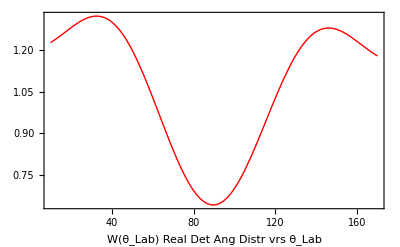

Real Detector is RED and Point Detector is GREEN

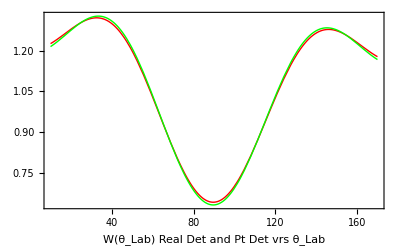

InterpolatingFunction[{{0.,180.}},<>]

(Real Det)/(Point Det) W(lab) vrs θ (in each frame)

shows inportance of overestimated real detector in data analysis

∞::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of indet will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {891/5} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {180} lies outside the range of data in the interpolating function. Extrapolation will be used.

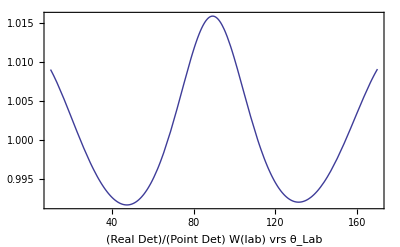

End

```mathematica
Print["XPlotLow and XPlotHigh are included because interpolation for real detectors extends lower than θ=0 and higher than θ=180, which is out of bounds in the fits above. Therfore, a limit on the ploting range of x values is necessary when interpolations involve division by complex infinities."]
XPlotLow=0+10
XPlotHigh=180-10

Do[WLab[x]=dummy2000[θDet[x]],{x,1,DetectorNumber,1}]

Print["Real Detector W(θ) in lab frame (Overestimated by integrating over all ϕ) for the detector angles defined"]
Do[WLabIntUnnorm[y]=NIntegrateInterpolatingFunction[dummy2001[x],{x,θDetMin[y],θDetMax[y]}],{y,1,6,1}]
Do[WLabIntNormFact[y]=Integrate[Sin[x],{x,θDetMin[y],θDetMax[y]}],{y,1,DetectorNumber,1}]
Do[WLabInt[y]=WLabIntUnnorm[y]/WLabIntNormFact[y],{y,1,DetectorNumber,1}]
Print["Detθ   WLabPtDet    WLabInt     WLabInt/WLabPtDet"]
Do[Print[θDet[y],"   ",WLab[y],"   ",WLabInt[y],"    ",WLabInt[y]/WLab[y]],{y,1,DetectorNumber,1}]

Print["Real Detector W(θ) in lab frame (Overestimated by integrating over all ϕ) for plotting"]
Print["Numerically integrating over laboratory distribution for 100 overestimated real detectors for plotting purposes"]
Do[WLabIntUnnormPlot[y]=NIntegrateInterpolatingFunction[dummy2001[x],{x,y-MaxEntryAngle,y+MaxEntryAngle}],{y,0,π,π/100}]
(*Do[Print[WLabIntUnnormPlot[y]],{y,0,π,π/100}]*)
Do[WLabIntNormFactPlot[y]=Integrate[Sin[x],{x,y-MaxEntryAngle,y+MaxEntryAngle}],{y,0,π,π/100}]
(*Do[Print[WLabIntNormFactPlot[y]],{y,0,π,π/100}]*)
Do[WLabIntPlot[y]=WLabIntUnnormPlot[y]/WLabIntNormFactPlot[y],{y,0,π,π/100}]
(*Do[Print[WLabIntPlot[y]],{y,0,π,π/100}]*)

Wlabintegratedplot:=Table[{θ*180/π,WLabIntPlot[θ]},{θ,0,π,π/100}]

Plot[Evaluate[Interpolation[Wlabintegratedplot]][x],{x,XPlotLow,XPlotHigh},
Frame->True, PlotRange->All,
FrameLabel-> "W(θ_Lab) Real Det Ang Distr vrs θ_Lab",PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,1,0]}}]

Print["Real Detector is RED and Point Detector is GREEN"]
Plot[{Evaluate[Interpolation[Wlabintegratedplot]][x],Evaluate[Interpolation[dummy1000]][x]},{x,XPlotLow,XPlotHigh},
Frame->True, PlotRange->All,
FrameLabel-> "W(θ_Lab) Real Det and Pt Det vrs θ_Lab",PlotStyle->{{RGBColor[1,0,0]},{RGBColor[0,1,0]}}]

dummy5001=Interpolation[Wlabintegratedplot]

dummy5000:=Table[{θ,dummy5001[θ]/dummy2000[θ]},{θ,0,180,180/100}]

Print["(Real Det)/(Point Det) W(lab) vrs θ (in each frame)"]
Print["shows inportance of overestimated real detector in data analysis"]
Plot[Evaluate[Interpolation[dummy5000]][x],{x,XPlotLow,XPlotHigh},
Frame->True, PlotRange->All,
FrameLabel-> "(Real Det)/(Point Det) W(lab) vrs θ_Lab"]

Print["End"]
```

```mathematica
Print["Section for DATA, ERRORS, and Theoretical Curves"]
(* DATA and ERRORS and PLOTS *)
(*data by Charles for Jurosphere*)
(*
data={
{157.6,1.17,.02},
{133.57,1.08,.03},
{107.94,.9,.1},
{94.16,.8,.1},
{85.84,.8,.2},
{72.05,.87,.01}
}
*)
(* data from EPJ A Back et al *)
(*
datapointcount=4
scalefactor=0.988
angle[1]=78
angle[2]=101
angle[3]=133.6
angle[4]=157.6
counts[1]=0.9*scalefactor
counts[2]=0.88*scalefactor
counts[3]=1.13*scalefactor
counts[4]=1.12*scalefactor
error[1]=0.05
error[2]=0.05
error[3]=0.04
error[4]=0.05
data={
{angle[1],counts[1],error[1]},
{angle[2],counts[2],error[2]},
{angle[3],counts[3],error[3]},
{angle[4],counts[4],error[4]}
}
*)

(* Data for Adam Hecth *)
datapointcount=4
scalefactor=1.0
angle[1]=50
angle[2]=90
angle[3]=126
angle[4]=160
(*for L=2 2 to 0 transition *)
(*
counts[1]=1.1*scalefactor
counts[2]=0.79*scalefactor
counts[3]=1.03*scalefactor
counts[4]=1.17*scalefactor
*)
(* for L=2 adam paper *)
counts[1]=WLabInt[1]*scalefactor
counts[2]=WLabInt[2]*scalefactor
counts[3]=WLabInt[3]*scalefactor
counts[4]=WLabInt[4]*scalefactor
error[1]=0.05
error[2]=0.05
error[3]=0.04
error[4]=0.05
data={
{angle[1],counts[1],error[1]},
{angle[2],counts[2],error[2]},
{angle[3],counts[3],error[3]},
{angle[4],counts[4],error[4]}
}
dataForFitting={
{angle[1],counts[1]},
{angle[2],counts[2]},
{angle[3],counts[3]},
{angle[4],counts[4]}
}


Print["Data and Error shown with W(θ_Lab) versus θ_Lab for Point Detectors ***AND*** W(θ_Nuclear) versus θ_Nuclear (GREY DASHED)"]
DisplayTogether[ParametricPlot[{LabTest*(180/π),γ^2*(1+β*Cos[θ])^2*PointDetDistribution},{θ,0,π},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel-> "W(θ_Lab) and W(θ_Nuclear) Pt Det vrs θ_Lab",
PlotStyle->{RGBColor[1,0,0]},
AxesLabel->{"θ_Lab (degree)","W(θ) (1/sr)"}],
ParametricPlot[{(180/π)*θ,PointDetDistribution},{θ,0,π},PlotStyle->{GrayLevel[0],Dashing[{.03}]}],ErrorListPlot[data,PlotStyle->{Hue[0],PointSize[.03]}]
]

Print["Data and Error shown with W(θ_Lab) versus θ_Lab for Overestimated Real Detectors  (RED) ***AND*** W(θ_Nuclear) versus θ_Nuclear (GREY DASHED)"]
DisplayTogether[
Plot[Evaluate[Interpolation[Wlabintegratedplot]][x],{x,XPlotLow,XPlotHigh},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel-> "W(θ_Lab) and W(θ_Nuclear) Real Det vrs θ_Lab",PlotStyle->{RGBColor[1,0,0]}],
ParametricPlot[{(180/π)*θ,Distribution},{θ,0,π},PlotStyle->{GrayLevel[0],Dashing[{.03}]}],ErrorListPlot[data,PlotStyle->{Hue[0],PointSize[.03]}]
]


Print["χ^2/N for the data points compared with W(θ_Lab) for Real Detectors (Not Point Detectors)"]
chi=(∑_(i=1)^datapointcount ((counts[i]-Evaluate[Interpolation[Wlabintegratedplot]][angle[i]])/error[i])^2)/datapointcount


Print["Fit to Legendre Polynomials for a[0] and a[2] only"]
FitToLTwo=Fit[dataForFitting,
{LegendreP[0,Cos[θ*π/180]],LegendreP[2,Cos[θ*π/180]]},
θ]

Print["Fit to Legendre Polynomials for a[0], a[2], and a[4] only"]
FitToLTwoFour=Fit[dataForFitting,
{LegendreP[0,Cos[θ*π/180]],LegendreP[2,Cos[θ*π/180]],LegendreP[4,Cos[θ*π/180]]},
θ]

Print["a[λ] normalized to a[0] from earlier nuclear frame calculation: (from 0 to 4 ONLY) "]
Do[Print[a[λ]/a[0]],{λ,0,4,1}]

(* Not working becaused I can't pull off the coefficients from the fit just yet *)
(*
Print["χ^2/N for the data points fir to LegendreP[2,Cos[θ]] compared to "]
chiForFitTwo=((FitToLTwo-a[2])/a[2])^2
*)

Print["Data and Error shown with W(θ_Lab) versus θ_Lab for Overestimated Real Detectors (RED) ***AND*** and W(θ_Nuclear) versus θ_Nuclear (GREY DASHED) ***AND*** the fit of the data to Legendre Polynomials of Rank 0 and 2 ONLY (BLUE)"]
DisplayTogether[
Plot[Evaluate[Interpolation[Wlabintegratedplot]][x],{x,XPlotLow,XPlotHigh},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel-> "W(θ_Lab) and W(θ_Nuclear) Real Det vrs θ_Lab",PlotStyle->{RGBColor[1,0,0]}],
ParametricPlot[{(180/π)*θ,Distribution},{θ,0,π},PlotStyle->{GrayLevel[0],Dashing[{.03}]}],ErrorListPlot[data,PlotStyle->{Hue[0],PointSize[.03]}],
Plot[FitToLTwo,{θ,0,180},PlotStyle->{RGBColor[0,0,1]}]
]

Print["Data and Error shown with W(θ_Lab) versus θ_Lab for Overestimated Real Detectors (RED) ***AND*** and W(θ_Nuclear) versus θ_Nuclear (GREY DASHED) ***AND*** the fit of the data to Legendre Polynomials of Rank 0 and 2 and 4 ONLY (BLUE)"]
DisplayTogether[
Plot[Evaluate[Interpolation[Wlabintegratedplot]][x],{x,XPlotLow,XPlotHigh},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel-> "W(θ_Lab) and W(θ_Nuclear) Real Det vrs θ_Lab",PlotStyle->{RGBColor[1,0,0]}],
ParametricPlot[{(180/π)*θ,Distribution},{θ,0,π},PlotStyle->{GrayLevel[0],Dashing[{.03}]}],ErrorListPlot[data,PlotStyle->{Hue[0],PointSize[.03]}],
Plot[FitToLTwoFour,{θ,0,180},PlotStyle->{RGBColor[0,0,1]}]
]

Print["End"]
```

Section for DATA, ERRORS, and Theoretical Curves

4

1.

50

90

126

160

0.914689

0.712964

0.825583

1.88577

0.05

0.05

0.04

0.05

{{50,0.914689,0.05},{90,0.712964,0.05},{126,0.825583,0.04},{160,1.88577,0.05}}

{{50,0.914689},{90,0.712964},{126,0.825583},{160,1.88577}}

Data and Error shown with W(θ_Lab) versus θ_Lab for Point Detectors ***AND*** W(θ_Nuclear) versus θ_Nuclear (GREY DASHED)

⁃Graphics⁃

Data and Error shown with W(θ_Lab) versus θ_Lab for Overestimated Real Detectors  (RED) ***AND*** W(θ_Nuclear) versus θ_Nuclear (GREY DASHED)

⁃Graphics⁃

χ^2/N for the data points compared with W(θ_Lab) for Real Detectors (Not Point Detectors)

1.16205×10^-10

Fit to Legendre Polynomials for a[0] and a[2] only

0.978174+0.921688 (-1/2+3/2 Cos[(π θ)/180]^2)

Fit to Legendre Polynomials for a[0], a[2], and a[4] only

0.983393+0.854866 (-1/2+3/2 Cos[(π θ)/180]^2)+0.416712 (3/8-15/4 Cos[(π θ)/180]^2+35/8 Cos[(π θ)/180]^4)

a[λ] normalized to a[0] from earlier nuclear frame calculation: (from 0 to 4 ONLY)

1.

8.4396×10^-21

0.923159

7.10986×10^-19

0.468843

Data and Error shown with W(θ_Lab) versus θ_Lab for Overestimated Real Detectors (RED) ***AND*** and W(θ_Nuclear) versus θ_Nuclear (GREY DASHED) ***AND*** the fit of the data to Legendre Polynomials of Rank 0 and 2 ONLY (BLUE)

⁃Graphics⁃

Data and Error shown with W(θ_Lab) versus θ_Lab for Overestimated Real Detectors (RED) ***AND*** and W(θ_Nuclear) versus θ_Nuclear (GREY DASHED) ***AND*** the fit of the data to Legendre Polynomials of Rank 0 and 2 and 4 ONLY (BLUE)

⁃Graphics⁃

End

The value of PlotPoints given in this evaluation may cause delay in displaying the graphic. Reducing the value of the PlotPoints option may help.

```mathematica
Print["Lab versus Nuclear Frame Geometries"]

(* Lab versus CM angle *)
Print["θ_lab versus θ_nuclear"]
ParametricPlot[{θ*(180/π),LabTest*(180/π)},{θ,0,π},
Frame->True, PlotRange->All,PlotPoints->180,
AxesOrigin->{0,0},
PlotLabel-> "Lab θ versus Nucl Frame θ",
AxesLabel->{"θ_Nuclear (degree)","θ_Lab (degree)"}]

Print["θ_lab/θ_nuclear versus θ_nuclear"]
ParametricPlot[{θ*(180/π),LabTest/θ},{θ,0,π},
Frame->True, PlotRange->All,PlotPoints->180,
AxesOrigin->{0,0},
PlotLabel-> "Lab θ vrs Nucl Frame θ (Fraction)",
AxesLabel->{"θ_Nuclear (degree)","θ_Lab (degree)"}]

Print["W(θ_nuclear) versus θ_lab for point-like detector"]
ParametricPlot[{LabTest*(180/π),PointDetDistribution},{θ,0,π},
Frame->True, PlotRange->All,PlotPoints->180,
AxesOrigin->{0,0},
PlotLabel-> "W(θ) in Nucl Frame vrs Lab θ",
AxesLabel->{"θ_Nuclear (degree)","θ_Lab (degree)"}]

Print["(dΩ/dθ_lab) /(dΩ/dθ_nuclear) versus θ_nuclear for point-like detector"]
ParametricPlot[{θ*(180/π),γ^2*(1+β*Cos[θ])^2},{θ,0,π},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel-> "Solid Ang eff on W(Nuclear) vrs Nucl θ",
AxesLabel->{"θ_Lab (degree)","W(θ) (1/sr)"}]

Print["Full relativistic effects in W(θ_Lab) (solid angle and aberration as shown above)"]
ParametricPlot[{LabTest*(180/π),γ^2*(1+β*Cos[θ])^2},{θ,0,π},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel-> "Full Rel eff in Lab on W(Nuclear) vrs Lab θ",
AxesLabel->{"θ_Lab (degree)","W(θ) (1/sr)"}]

Print["Shown once again, W(θ_Lab) versus θ_lab for point-like detector (as above, but multiplied by W(θ_nuclear)"]
ParametricPlot[{LabTest*(180/π),γ^2*(1+β*Cos[θ])^2*PointDetDistribution},{θ,0,π},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel-> "Again, Pt Det Ang Distr vrs Lab Frame θ",
AxesLabel->{"θ_Lab (degree)","W(θ) (1/sr)"}]

(* as polar plot but as parametric plot where newx and newy are defined *)
(*
theta=ArcCos[LabTest]
radius=√((LabTest)^2+(γ^2*(1+β*Cos[θ])^2*PointDetDistribution)^2)
newx=radius*Cos[theta]
newy=radius*Sin[theta]
Do[dummyarraythree[θ]=ArcCos[newx/radius]*180/π,{θ,0,2π,π/20}]
Do[Print[dummyarraythree[θ]],{θ,0,π,π/10}]
Do[dummyarrayone[θ]=newx*180/π,{θ,0,2π,π/20}]
Do[Print[dummyarrayone[θ]],{θ,0,2π,π/20}]
Do[dummyarraytwo[θ]=newy,{θ,0,2π,π/20}]
Do[Print[dummyarraytwo[θ]],{θ,0,2π,π/20}]
ParametricPlot[{newx,newy},{θ,0,2π},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel-> "Point Det Ang Distr - Lab Frame"]
*)

(*
DistributionLabPolar=(1/a0)*a0*LegendreP[0,Cos[LabTest]]+(1/a0)*a2*LegendreP[2,Cos[LabTest]]+(1/a0)*a4*LegendreP[4,Cos[LabTest]]
PolarPlot[γ^2*(1+β*Cos[LabTest])^2*DistributionLabPolar,{θ,0,2π},
Frame->True,PlotRange->All]
*)
```

Lab versus Nuclear Frame Geometries

θ_lab versus θ_nuclear

⁃Graphics⁃

θ_lab/θ_nuclear versus θ_nuclear

⁃Graphics⁃

W(θ_nuclear) versus θ_lab for point-like detector

⁃Graphics⁃

(dΩ/dθ_lab) /(dΩ/dθ_nuclear) versus θ_nuclear for point-like detector

⁃Graphics⁃

Full relativistic effects in W(θ_Lab) (solid angle and aberration as shown above)

⁃Graphics⁃

Shown once again, W(θ_Lab) versus θ_lab for point-like detector (as above, but multiplied by W(θ_nuclear)

⁃Graphics⁃

```mathematica
Print["Doppler Shift information"]
(* Doppler Shift *)

Print["Doppler Shifted γ energy versus θ_Lab "]
ParametricPlot[{(180/π)*θ,γ*(1+β*Cos[θ])*Subscript[E, photonCM]},{θ,0,π},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel->"Doppler Shifted Gamma Energy",
AxesLabel->{"θ_Lab (degree)","Energy (MeV)"}]

Print["Doppler Shifted γ energy (Normalized) versus θ_Lab "]
ParametricPlot[{(180/π)*θ,γ*(1+β*Cos[θ])},{θ,0,π},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel->"Doppler Shifted γ En (Fraction)",
AxesLabel->{"θ_Lab (degree)","Energy (MeV)"}]

Print["Doppler Shifted γ energy versus θ_Lab for specific angles"]
Print["37 degrees"]
test37=γ*(1+β*Cos[37*π/180])*Subscript[E, photonCM]
Print["90 degrees"]
test90=Evaluate[γ*(1+β*Cos[90*π/180])*Subscript[E, photonCM]]
```

Doppler Shift information

Doppler Shifted γ energy versus θ_Lab

⁃Graphics⁃

Doppler Shifted γ energy (Normalized) versus θ_Lab

⁃Graphics⁃

Doppler Shifted γ energy versus θ_Lab for specific angles

37 degrees

1.66576

90 degrees

1.63059

```mathematica
Print["Section Not Working"]
(* as polar plot but as parametric plot where newx and newy are defined *)
(* NOT WORKING *)
(*
theta=ArcCos[LabTest]
radius=√((LabTest)^2+(γ^2*(1+β*Cos[θ])^2*PointDetDistribution)^2)
newx=radius*LabTest
newy=radius*Sin[theta]
Do[dummyarraythree[θ]=ArcCos[newx/radius],{θ,0,2π,π/20}]
Print["Labtest"]
Do[Print[LabTest],{θ,0,π,π/10}]
Print["dummyarraythree"]
Do[Print[dummyarraythree[θ]],{θ,0,π,π/10}]
Do[dummyarrayone[θ]=newx*180/π,{θ,0,2π,π/20}]
Do[Print[dummyarrayone[θ]],{θ,0,2π,π/20}]
Do[dummyarraytwo[θ]=newy,{θ,0,2π,π/20}]
Do[Print[dummyarraytwo[θ]],{θ,0,2π,π/20}]
ParametricPlot[{newx,newy},{θ,0,2π},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel-> "Point Det Ang Distr - Lab Frame"]
*)
```

Section Not Working

```mathematica
Print["New Section for Lab Angle Ratios:"]
(*New Section for Lab Angle Ratios: *)
(* for angles of 90 enter 90.0000000001 due to problems with tangent below *)

x:=157*π/180
y1=If[ArcTan[Sin[x]/(γ*(Cos[x]+β))]>0,ArcCos[(-β γ^2 Tan[x]^2+√(1+γ^2 Tan[x]^2-β^2 γ^2 Tan[x]^2))/(1+γ^2 Tan[x]^2)],ArcCos[(-β γ^2 Tan[x]^2-√(1+γ^2 Tan[x]^2-β^2 γ^2 Tan[x]^2))/(1+γ^2 Tan[x]^2)]]
y1deg=y1*180/π
Print["D1"]
D1=γ^2*(1+β*Cos[y1])^2*(∑_(λ=0)^10 (1/a[0])*a[λ]*LegendreP[λ,Cos[y1]])

x:=94*π/180
y2=If[ArcTan[Sin[x]/(γ*(Cos[x]+β))]>0,ArcCos[(-β γ^2 Tan[x]^2+√(1+γ^2 Tan[x]^2-β^2 γ^2 Tan[x]^2))/(1+γ^2 Tan[x]^2)],ArcCos[(-β γ^2 Tan[x]^2-√(1+γ^2 Tan[x]^2-β^2 γ^2 Tan[x]^2))/(1+γ^2 Tan[x]^2)]]
y2deg=y2*180/π
Print["D2"]
D2=γ^2*(1+β*Cos[y1])^2*(∑_(λ=0)^10 (1/a[0])*a[λ]*LegendreP[λ,Cos[y2]])

Print["Ratio="]
Ratio=D1/D2
```

New Section for Lab Angle Ratios:

2.75552

157.88

D1

1.12966

1.68047

96.2837

D2

0.769585

Ratio=

1.46788

```mathematica
Print[" Calculate Distribution for particular angle in the nuclear frame and in the laboratory frame"](* Calculate Distribution for particular angle in the nuclear frame and in the laboratory frame *)

x=154 (* Angle of Detector *)
(* For Angles of 90, enter 90.00000000000001 *)
(* Problem with Tangent below *)

Print["In Nuclear Frame"]
y1=x*π/180
Print["D1"]
D1=(∑_(λ=0)^10 (1/a[0])*a[λ]*LegendreP[λ,Cos[y1]])
y2=If[ArcTan[Sin[y1]/(γ*(Cos[y1]+β))]>0,ArcCos[(-β γ^2 Tan[y1]^2+√(1+γ^2 Tan[y1]^2-β^2 γ^2 Tan[y1]^2))/(1+γ^2 Tan[y1]^2)],ArcCos[(-β γ^2 Tan[y1]^2-√(1+γ^2 Tan[y1]^2-β^2 γ^2 Tan[y1]^2))/(1+γ^2 Tan[y1]^2)]]
Print["In Laboratory Frame"]
Print["Effective Nuclear Angle of Gamma Emmision"]
y2deg=y2*180/π
Print["D2"]
D2=γ^2*(1+β*Cos[y1])^2*(∑_(λ=0)^10 (1/a[0])*a[λ]*LegendreP[λ,Cos[y2]])
```

Calculate Distribution for particular angle in the nuclear frame and in the laboratory frame

154

In Nuclear Frame

(77 π)/90

D1

1.51474

2.6995

In Laboratory Frame

Effective Nuclear Angle of Gamma Emmision

154.67

D2

1.45639

```mathematica
Print["Plots of a[4] versus a[2] for various values of the mixing ration, δ, for a fixed σ (distribution of magnetic substates)

Important!!!

The σ for this section is defined in the first section above!!!

Gain an understanding of the σ you would like to run with from the section below"]

(* Plots of a[4] versus a[2] for various values of the mixing ration, δ *)

(*Print["Printing FLambda[λ]= for 0 to 10"]*)
Do[FLambda[λ]=0,{λ,0,10,1}]
Do[FLambda[λ]=1/(1+delta^2)*((-1^(Subscript[J, i]+Subscript[J, f]-1))((2λ+1)(2L+1)(2L+1)(2 Subscript[J, i]+1))^(1/2)Check[ThreeJSymbol[{L,1},{L,-1},{λ,0}],0]Check[SixJSymbol[{L,L,λ},{Subscript[J, i],Subscript[J, i],Subscript[J, f]}],0]
+2*delta*(-1^(Subscript[J, i]+Subscript[J, f]-1))((2λ+1)(2L+1)(2(L+1)+1)(2 Subscript[J, i]+1))^(1/2)Check[ThreeJSymbol[{L,1},{(L+1),-1},{λ,0}],0]Check[SixJSymbol[{L,(L+1),λ},{Subscript[J, i],Subscript[J, i],Subscript[J, f]}],0]
+delta^2(-1^(Subscript[J, i]+Subscript[J, f]-1))((2λ+1)(2(L+1)+1)(2(L+1)+1)(2 Subscript[J, i]+1))^(1/2)Check[ThreeJSymbol[{(L+1),1},{(L+1),-1},{λ,0}],0]Check[SixJSymbol[{(L+1),(L+1),λ},{Subscript[J, i],Subscript[J, i],Subscript[J, f]}],0]),{λ,0,10,1}]
(*Do[Print[FLambda[λ]],{λ,0,10,1}]*)

Do[a[λ]=0,{λ,0,10,1}]
(*Print["Printing a[λ]= for 0 to 10 (coefficients for Legrende Polynomials)"]*)

Do[a[λ]=B[λ]FLambda[λ]Q[λ]U[λ],{λ,0,10,1}]

(*Do[Print[a[λ]],{λ,0,10,1}]*)

Print[" Plots of a[4] versus a[2] for various values of the mixing ration, δ "]

(* Plots! *)
ParametricPlot[{a[2]/a[0],a[4]/a[0]},{delta,-100,100},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel-> "a[4] versus a[2]"]

DisplayTogether[
ParametricPlot[{a[2]/a[0],a[4]/a[0]},{delta,-100,100},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel-> "a[4] versus a[2]"],
ParametricPlot[{a[2]/a[0],a[4]/a[0]},{delta,-1.01,-0.09},PlotStyle->{Thickness[0.02],RGBColor[1,0,0]}],
ParametricPlot[{a[2]/a[0],a[4]/a[0]},{delta,-0.01,0.01},PlotStyle->{Thickness[0.02],RGBColor[0,1,0]}],
ParametricPlot[{a[2]/a[0],a[4]/a[0]},{delta,0.99,1.01},PlotStyle->{Thickness[0.02],RGBColor[0,0,1]}]
]
Print["Red is -1.01<δ<-0.99   Green is -.01<δ<.01    Blue is 0.99<δ<1.00"]
```

Plots of a[4] versus a[2] for various values of the mixing ration, δ, for a fixed σ (distribution of magnetic substates)  Important!!!  The σ for this section is defined in the first section above!!!  Gain an understanding of the σ you would like to run with from the section below

ClebschGordan::tri: ThreeJSymbol[{1, 1}, {2, -1}, {0, 0}] is not triangular.

ClebschGordan::tri: SixJSymbol[{1, 2, 0}, {16, 16, 15}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1, 1}, {1, -1}, {3, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: "tri" will be suppressed during this calculation.

Plots of a[4] versus a[2] for various values of the mixing ration, δ

⁃Graphics⁃

⁃Graphics⁃

Red is -1.01<δ<-0.99   Green is -.01<δ<.01    Blue is 0.99<δ<1.00

```mathematica
Print["Plots of a[4] versus a[2] for various values of the level width, σ"]
Null

Print["This allows one to narrow down choices for σ set as a parameter in the first section of the notebook.  Once this is narrowed down one can iterate the deltaplot or sigma more carefully and determine distributions in the laboratory frame.\n\nPick out the m-substate distribution type below with the parathesis comments of Mathematica.\n\nImportant!!!\n\nKill Kernal and Rerun Each time you want to run this section!!!\n\n(for reasons I don't fully understand, believing it runs into the questions around g[m])\n\nThen Kill Kernal and rerun everything once you have an understanding of the σ and δ you would like to run with.\n\nTo try different values of deltaPlot, run the section that follows this!\n\nYou should try to obtain σ/\!\(\*SubscriptBox[\(J\), \(i\)]\) experimentally from a pure transition (δ=0)!"]

Do[g[m]=0,{m,-Subscript[J, i],Subscript[J, i],1}]
Do[gMax[m]=0,{m,-Subscript[J, i],Subscript[J, i],1}]
Do[RhoLambdaPlot[λ]=0,{λ,0,10,1}]
Do[BPlot[λ]=0,{λ,0,10,1}]
Do[FLambdaPlot[λ]=0,{λ,0,10,1}]
Do[aPlot[λ]=0,{λ,0,10,1}]
Null
Null
Null

Do[gunnorm[m]=ⅇ^(-m^2/(2 σplot^2)),{m,-Subscript[J, i],Subscript[J, i],1}]
gunnormplot[x]=ⅇ^(-x^2/(2 σplot^2))
Do[gMaxunnorm[m]=ⅇ^(-m^2/(2 0.01^2)),{m,-Subscript[J, i],Subscript[J, i],1}]
Null
Null
Null

(*
Do[gunnorm[m]=ⅇ^(-(Subscript[J, i]-Abs[m])^2/(2 σplot^2)),{m,-Subscript[J, i],Subscript[J, i],1}] gunnormplot[x]=ⅇ^(-(Subscript[J, i]-Abs[x])^2/(2 σplot^2)) Do[gMaxunnorm[m]=ⅇ^(-(Subscript[J, i]-Abs[m])^2/(2 0.01^2)),{m,-Subscript[J, i],Subscript[J, i],1}]
*)
Null

(*
Do[gunnorm[m]=ⅇ^(-(Subscript[J, i]-m)^2/(2 σplot^2)),{m,-Subscript[J, i],Subscript[J, i],1}] gunnormplot[x]=ⅇ^(-(Subscript[J, i]-x)^2/(2 σplot^2)) Do[gMaxunnorm[m]=ⅇ^(-(Subscript[J, i]-m)^2/(2 0.01^2)),{m,-Subscript[J, i],Subscript[J, i],1}]
*)
Null

(*This can be from cross sections to the magnetic substates populated in single-nucleon knowckout reactions since these can be calculated*)
(*
Print["hand-input g[m]"] gunnorm[5/2]=gunnorm[-5/2]=12.8 (gunnorm[3/2]=gunnorm[-3/2]=6.6 (gunnorm[1/2]=gunnorm[-1/2]=5.7 Do[gMaxunnorm[m]=ⅇ^(-(Subscript[J, i]-Abs[m])^2/(2 0.01^2)),{m,-Subscript[J, i],Subscript[J, i],1}] (gunnormplot=1+x+x^2)))(*actually will not work for plotting purposes below*)
*)
Null

(*
Do[gunnorm[m]=1/(2 Subscript[J, i]+1),{m,-Subscript[J, i],Subscript[J, i],1}]
*)
Null

(*
Do[gunnorm[m]=0,{m,-Subscript[J, i],Subscript[J, i],1}] gunnorm[0]=1
*)
Null

NormalizeGm:=∑_(m=-Subscript[J, i])^Subscript[J, i] gunnorm[m]
NormalizeGmMax:=∑_(m=-Subscript[J, i])^Subscript[J, i] gMaxunnorm[m]
Do[g[m]=gunnorm[m]/NormalizeGm,{m,-Subscript[J, i],Subscript[J, i],1}]
Do[gMax[m]=gMaxunnorm[m]/NormalizeGmMax,{m,-Subscript[J, i],Subscript[J, i],1}]
(*
Print["list of magnetic substates from -\!\(\*SubscriptBox[\(J\), \(i\)]\) to \!\(\*SubscriptBox[\(J\), \(i\)]\)"] Do[Print[m],{m,-Subscript[J, i],Subscript[J, i],1}] Print["list of normalized magnetic substate populations from -\!\(\*SubscriptBox[\(J\), \(i\)]\) to \!\(\*SubscriptBox[\(J\), \(i\)]\)"] Do[Print[g[m]],{m,-Subscript[J, i],Subscript[J, i],1}] plottableg=Table[g[m],{m,-Subscript[J, i],Subscript[J, i],1}] ListPlot[plottableg]
*)
(*
plottableg=Table[{m,g[m]},{m,-Subscript[J, i],Subscript[J, i],1}]
*)
(*
ListPlot[plottableg,Joined->True,PlotLabel->"g[m] population plot"]

Plot[Evaluate[Interpolation[plottableg]][x],{x,-Subscript[J, i],Subscript[J, i]},Frame->True,PlotRange->All,AxesOrigin->{0,0},PlotLabel->"g[m] population plot",PlotStyle->{RGBColor[1,0,0]}]
*)
(* *)

Do[RhoLambdaPlot[λ]=∑_(m=-Subscript[J, i])^Subscript[J, i] (-1)^(Subscript[J, i]+m) √(2 λ+1) Check[ThreeJSymbol[{Subscript[J, i],-m},{Subscript[J, i],m},{λ,0}],0] g[m],{λ,0,10,1}]
Do[BPlot[λ]=√(2 Subscript[J, i]+1) RhoLambdaPlot[λ],{λ,0,10,1}]

(*Print["Printing FLambda[λ]= for 0 to 10"]*)
Do[FLambdaPlot[λ]=0,{λ,0,10,1}]
Do[FLambdaPlot[λ]=1/(1+deltaPlot^2)(-1^(Subscript[J, i]+Subscript[J, f]-1) √((2 λ+1) (2 L+1) (2 L+1) (2 Subscript[J, i]+1)) Check[ThreeJSymbol[{L,1},{L,-1},{λ,0}],0] Check[SixJSymbol[{L,L,λ},{Subscript[J, i],Subscript[J, i],Subscript[J, f]}],0]+2 deltaPlot (-1^(Subscript[J, i]+Subscript[J, f]-1)) √((2 λ+1) (2 L+1) (2 (L+1)+1) (2 Subscript[J, i]+1)) Check[ThreeJSymbol[{L,1},{L+1,-1},{λ,0}],0] Check[SixJSymbol[{L,L+1,λ},{Subscript[J, i],Subscript[J, i],Subscript[J, f]}],0]+deltaPlot^2 (-1^(Subscript[J, i]+Subscript[J, f]-1)) √((2 λ+1) (2 (L+1)+1) (2 (L+1)+1) (2 Subscript[J, i]+1)) Check[ThreeJSymbol[{L+1,1},{L+1,-1},{λ,0}],0] Check[SixJSymbol[{L+1,L+1,λ},{Subscript[J, i],Subscript[J, i],Subscript[J, f]}],0]),{λ,0,10,1}]
(*Do[Print[FLambdaPlot[λ]],{λ,0,10,1}]*)

Do[aPlot[λ]=0,{λ,0,10,1}]
(*Print["Printing a[λ]= for 0 to 10 (coefficients for Legrende Polynomials)"]*)

Do[aPlot[λ]=BPlot[λ] FLambdaPlot[λ] Q[λ] U[λ],{λ,0,10,1}]

(*Do[Print[aPlot[λ]],{λ,0,10,1}]*)

Print[" Plots of a[4] versus a[2] for various values of the σ "]
Null

(*
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.1,100},Frame->True,PlotRange->All,AxesOrigin->{0,0},PlotLabel->"a[4] versus a[2]"]
*)
Print["deltaPlot is what you have entered,  Red is 0.1*\!\(\*SubscriptBox[\(J\), \(i\)]\)<σplot<0.11*\!\(\*SubscriptBox[\(J\), \(i\)]\)   Yellow is 0.3*\!\(\*SubscriptBox[\(J\), \(i\)]\)<σplot<0.31*\!\(\*SubscriptBox[\(J\), \(i \(\(\\\)\( \)\(\\\)\( \)\(\\\)\( \)\(\\\)\( \)\(\\\)\( \)\(\\\)\( \)\)\)]\)Green is 0.5*\!\(\*SubscriptBox[\(J\), \(i\)]\)<σplot<0.51*\!\(\*SubscriptBox[\(J\), \(i\)]\)    Turquoise is 0.7*\!\(\*SubscriptBox[\(J\), \(i\)]\)<σplot<0.71*\!\(\*SubscriptBox[\(J\), \(i\)]\)     Blue is 0.9*\!\(\*SubscriptBox[\(J\), \(i\)]\)<σplot<0.91*\!\(\*SubscriptBox[\(J\), \(i\)]\)"]
Do[
DisplayTogether[
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.1,100},Frame->True,PlotRange->All,AxesOrigin->{0,0},PlotLabel->"a[4] versus a[2]"],
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.1 Subscript[J, i],0.11 Subscript[J, i]},PlotStyle->{Thickness[0.02],RGBColor[1,0,0]}],
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.3 Subscript[J, i],0.31 Subscript[J, i]},PlotStyle->{Thickness[0.02],RGBColor[1,1,0]}],
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.5 Subscript[J, i],0.51 Subscript[J, i]},PlotStyle->{Thickness[0.02],RGBColor[0,1,0]}],
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.7 Subscript[J, i],0.71 Subscript[J, i]},PlotStyle->{Thickness[0.02],RGBColor[0,1,1]}],
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.9 Subscript[J, i],0.91 Subscript[J, i]},PlotStyle->{Thickness[0.02],RGBColor[0,0,1]}]
],
{deltaPlot,-1,1,0.2}]

Print["deltaPlot is what you have entered,  Red is 0.1*\!\(\*SubscriptBox[\(J\), \(i\)]\)<σplot<0.11*\!\(\*SubscriptBox[\(J\), \(i\)]\)   Yellow is 0.3*\!\(\*SubscriptBox[\(J\), \(i\)]\)<σplot<0.31*\!\(\*SubscriptBox[\(J\), \(i \(\(\\\)\( \)\(\\\)\( \)\(\\\)\( \)\(\\\)\( \)\(\\\)\( \)\(\\\)\( \)\)\)]\)Green is 0.5*\!\(\*SubscriptBox[\(J\), \(i\)]\)<σplot<0.51*\!\(\*SubscriptBox[\(J\), \(i\)]\)    Turquoise is 0.7*\!\(\*SubscriptBox[\(J\), \(i\)]\)<σplot<0.71*\!\(\*SubscriptBox[\(J\), \(i\)]\)     Blue is 0.9*\!\(\*SubscriptBox[\(J\), \(i\)]\)<σplot<0.91*\!\(\*SubscriptBox[\(J\), \(i\)]\)"]
```

Plots of a[4] versus a[2] for various values of the level width, σ

This allows one to narrow down choices for σ set as a parameter in the first section of the notebook.  Once this is narrowed down one can iterate the deltaplot or sigma more carefully and determine distributions in the laboratory frame.  Pick out the m-substate distribution type below with the parathesis comments of Mathematica.  Important!!!  Kill Kernal and Rerun Each time you want to run this section!!!  (for reasons I don't fully understand, believing it runs into the questions around g[m])  Then Kill Kernal and rerun everything once you have an understanding of the σ and δ you would like to run with.  To try different values of deltaPlot, run the section that follows this!  You should try to obtain σ/J_i experimentally from a pure transition (δ=0)!

General::spell1: Possible spelling error: new symbol name "BPlot" is similar to existing symbol "Plot".

General::spell1: Possible spelling error: new symbol name "aPlot" is similar to existing symbol "Plot".

ⅇ^(-x^2/(2 σplot^2))

ClebschGordan::tri: ThreeJSymbol[{3, 3}, {3, -3}, {7, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 2}, {3, -2}, {7, 0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{3, 1}, {3, -1}, {7, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: "tri" will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1, 1}, {2, -1}, {0, 0}] is not triangular.

ClebschGordan::tri: SixJSymbol[{1, 2, 0}, {3, 3, 2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1, 1}, {1, -1}, {3, 0}] is not triangular.

General::stop: Further output of ClebschGordan :: "tri" will be suppressed during this calculation.

Plots of a[4] versus a[2] for various values of the σ

deltaPlot is what you have entered,  Red is 0.1*J_i<σplot<0.11*J_i   Yellow is 0.3*J_i<σplot<0.31*J_i\ \ \ \ \ \ Green is 0.5*J_i<σplot<0.51*J_i    Turquoise is 0.7*J_i<σplot<0.71*J_i     Blue is 0.9*J_i<σplot<0.91*J_i

deltaPlot is what you have entered,  Red is 0.1*J_i<σplot<0.11*J_i   Yellow is 0.3*J_i<σplot<0.31*J_i\ \ \ \ \ \ Green is 0.5*J_i<σplot<0.51*J_i    Turquoise is 0.7*J_i<σplot<0.71*J_i     Blue is 0.9*J_i<σplot<0.91*J_i

```mathematica
Print["Play with this section rather than above for various values of deltaplot!"]

Print["Note that a4 versus a2 will still be an eliptical (of sorts) function of δ and will vary accordingly for different values of deltaPlot below."]

Print["deltaPlot="]
deltaPlot=-1

DisplayTogether[
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.1,100},
Frame->True, PlotRange->All,
AxesOrigin->{0,0},
PlotLabel-> "a[4] versus a[2]"],
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.1*Subscript[J, i],0.11*Subscript[J, i]},PlotStyle->{Thickness[0.02],RGBColor[1,0,0]}],
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.3*Subscript[J, i],0.31*Subscript[J, i]},PlotStyle->{Thickness[0.02],RGBColor[1,1,0]}],
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.5*Subscript[J, i],0.51*Subscript[J, i]},PlotStyle->{Thickness[0.02],RGBColor[0,1,0]}],
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.7*Subscript[J, i],0.71*Subscript[J, i]},PlotStyle->{Thickness[0.02],RGBColor[0,1,1]}],
ParametricPlot[{aPlot[2]/aPlot[0],aPlot[4]/aPlot[0]},{σplot,0.9*Subscript[J, i],0.91*Subscript[J, i]},PlotStyle->{Thickness[0.02],RGBColor[0,0,1]}]
]

Print["deltaPlot is what you have entered,  Red is 0.1*J_i<σplot<0.11*J_i   Yellow is 0.3*J_i<σplot<0.31*J_(i \ \ \ \ \ \)Green is 0.5*J_i<σplot<0.51*J_i    Turquoise is 0.7*J_i<σplot<0.71*J_i     Blue is 0.9*J_i<σplot<0.91*J_i"]

ContourPlot[aPlot[2]/aPlot[0],{σplot,0.1,Subscript[J, i]},{deltaPlot,-5,5},
PlotPoints->30,
Contours->15,
AxesLabel->{"σ","δ"},
PlotLabel-> "a2 versus σ and δ"]

a2meshplot=Plot3D[
aPlot[2]/aPlot[0],
{σplot,0.1,Subscript[J, i]},{deltaPlot,-5,5},
PlotPoints->30,
ImageSize->400,
SphericalRegion->True,
Boxed->True,
Axes->True,
PlotRange->All,
ColorFunction->Hue,
AxesLabel->{"σ","δ","a2"}
]
Show[a2meshplot,ViewPoint->{-2,0,0}]
Show[a2meshplot,ViewPoint->{-2,0,2}]

ContourPlot[aPlot[4]/aPlot[0],{σplot,0.1,Subscript[J, i]},{deltaPlot,-5,5},
PlotPoints->30,
Contours->15,
AxesLabel->{"σ","δ"},
PlotLabel-> "a4 versus σ and δ"]

a4meshplot=Plot3D[
aPlot[4]/aPlot[0],
{σplot,0.1,Subscript[J, i]},{deltaPlot,-5,5},
PlotPoints->30,
ImageSize->400,
SphericalRegion->True,
Boxed->True,
Axes->True,
PlotRange->All,
ColorFunction->Hue,
AxesLabel->{"σ","δ","a4"}
]
Show[a4meshplot,ViewPoint->{-2,0,0}]
Show[a4meshplot,ViewPoint->{-2,0,2}]

ContourPlot[aPlot[4]/aPlot[2],{σplot,0.1,Subscript[J, i]},{deltaPlot,-5,5},
PlotPoints->30,
Contours->15,
AxesLabel->{"σ","δ"},
PlotLabel-> "a4/a2 versus σ and δ"]

a2a4meshplot=Plot3D[
aPlot[4]/aPlot[2],
{σplot,0.1,Subscript[J, i]},{deltaPlot,-5,5},
PlotPoints->30,
ImageSize->400,
SphericalRegion->True,
Boxed->True,
Axes->True,
PlotRange->All,
ColorFunction->Hue,
AxesLabel->{"σ","δ","a4/a2"}
]
Show[a2a4meshplot,ViewPoint->{-2,0,0}]
Show[a2a4meshplot,ViewPoint->{-2,0,2}]
```

Play with this section rather than above for various values of deltaplot!

Note that a4 versus a2 will still be an eliptical (of sorts) function of δ and will vary accordingly for different values of deltaPlot below.

deltaPlot=

-1

⁃Graphics⁃

deltaPlot is what you have entered,  Red is 0.1*J_i<σplot<0.11*J_i   Yellow is 0.3*J_i<σplot<0.31*J_i\ \ \ \ \ \ Green is 0.5*J_i<σplot<0.51*J_i    Turquoise is 0.7*J_i<σplot<0.71*J_i     Blue is 0.9*J_i<σplot<0.91*J_i

⁃ContourGraphics⁃

⁃SurfaceGraphics⁃

⁃SurfaceGraphics⁃

⁃SurfaceGraphics⁃

⁃ContourGraphics⁃

⁃SurfaceGraphics⁃

⁃SurfaceGraphics⁃

⁃SurfaceGraphics⁃

⁃ContourGraphics⁃

⁃SurfaceGraphics⁃

⁃SurfaceGraphics⁃

⁃SurfaceGraphics⁃